## Initialisation

### fixed parameters

define ionisation potential, electric field amplitude  (intensity), fundamental wavelength...

```mathematica
Ip=0.5;
R = Tan[π/4];
ω = 0.057;
prefactor = ((ⅈ / Sqrt[π])*(2*Ip)^(1/4));
```

### Define fields

electric  field  definition, vector potential, derivative of the action, action, ...

```mathematica
(*Define the electric field function as a 2D vector*)
E1[t_]:={Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2 t],0};
(*Define the vector potential components*)
Ax[tx_]:=-Integrate[E1[t][[1]],t]/. t->tx;
Ay[tx_]:=-Integrate[E1[t][[2]],t]/. t->tx;
(*Define the 2D vector potential A*)
A[tx_]:={Ax[tx],Ay[tx]};

(*Define Sf,Sfunc,DsFunc,D2sFunc,and action in terms of px,Ax,py,and Ay*)
Sf[tk_,p_List]=Integrate[2 (p[[1]]*Ax[t]+p[[2]]*Ay[t])+(Ax[t]^2+Ay[t]^2),t]/. t->tk;
(*Print[Sf[t,{px,py}]]*)
Sfunc[t_,p_List]:=0.5*Sf[t,p]+(0.5*(p[[1]]^2+p[[2]]^2)+Ip)*t;
(*Print[Sfunc[t,{px,py}]]*)
DsFunc[t_,p_List]:=D[Sfunc[tc,p],tc]/. tc->t;
(*Print[DsFunc[t,{px,py}]]*)
D2sFunc[t_,p_List]:=ω*D[Sfunc[tz,p],{tz,2}]/. tz->t;
(*Print[D2sFunc[t,{px,py}]]*)
action[t_,p_List]:=Exp[I*Sfunc[t,p]/ω];
(*Print[action[t,{px,py}]]*)
```

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

### Define the momentum grid

```mathematica
(*Define the range for px and py values*)
pxValues=Range[-2,2,0.1];
pyValues=Range[-2,2,0.1];
Print[Length[pxValues]]
Print[Length[pyValues]]
```

41

41

### Define plotting functions

```mathematica
(*Plot Ex and Ey and roots*)
plotEx:=Quiet[Plot[E1[t][[1]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotEy:=Quiet[Plot[E1[t][[2]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]];

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

SetDelayed::write: Tag Graphics in ()[filteredTValues_] is Protected.

### Create Grid of Seeds

```mathematica
(*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=3;
realSteps=20;imagSteps=20;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*Add the specific initial guess to the list of seeds*)
initialGuess=-2.0334+1.2321 ⅈ;
listofseeds=Prepend[listofseeds,initialGuess];

(*Ensure seeds are numerical values*)
listofseeds=N[listofseeds];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;
```

Find  all  the  roots for all px and py values (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_,seeds_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},
(*Find roots*)
allSolutions=Round[t/. Quiet[Table[FindRoot[DsFunc[t,{px,py}]==0,{t,tseed}],{tseed,seeds}]],0.0001];
complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];
(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,{px,py}]]]<=tolerance&&Abs[Im[DsFunc[#,{px,py}]]]<=tolerance&];
{filteredTValues}];
```

## CALCULATION : Saddle Point Solutions

```mathematica
Calculate all the time saddle point solutions value for corresponding px and py below
```

```mathematica
(*Generate results using the precise px and py values*)
results=
(*ParallelTable works similarly to Table,but it distributes the computation across multiple CPU cores,allowing for parallel execution and significantly speeding up the process.*)
ParallelTable[
generatePlotAndRoots[px,py,listofseeds],
{px,pxValues},{py,pyValues}
]
```

## rearrange data structure of the time arrays & prep them for plotting.

```mathematica
newResults=
Table[
{(*Calculate pxValue based on the index i*)
pxValue=-2+(i-1)*0.1,
(*Calculate pyValue based on the index j*)
pyValue=-2+(j-1)*0.1,
(*Extract the corresponding results for the current px and py values*)
results[[i,j]]},
(*Iterate over the length of the results list for both i and j*)
{i,Length[results]},{j,Length[results]}
];

(*Get the number of elements in each sub-array at the forth level*)
forthLevelCounts=Length/@#&/@#&/@#&/@newResults;
Print[forthLevelCounts];

(*Use Table to iterate over the nested arrays*)
Table[
Module[(*Use Module to create local variables px,py,and number*)
{px,py,number},
(*Assign the values of px,py,and number from the innerArray*)
{px,py,number}=innerArray;
(*Check if the first element of number is not equal to 4*)
If[First[number]=!=4,
Print["px: ",px,", py: ",py,", number: ",First[number]]
]
],
(*Iterate over each outerArray in forthLevelCounts*)
{outerArray,forthLevelCounts},
(*Iterate over each innerArray in the current outerArray*)
{innerArray,outerArray}];


(*Flatten the newResults list by one level to get a list of sublists, Map over each sublist in flattenedResults For each sublist elem,join the first two elements with the elements of the nested list inside the third element.*)
tsExtended=Map[Function[{elem},Join[{elem[[1]],elem[[2]]},elem[[3,1]]]],Flatten[newResults,1]];
(*so essentially grabbing px and py and putting them in the same array as the time saddle point solutions ts1,ts2,ts3,ts4 so the array of arrays will look like {{px,py,ts1,ts2,ts3,ts4},repeat for different values of px and py}*)

(*-validData is a list of lists where each sublist contains four elements {Real part of ts,Imaginary part of ts,px,py}.*)
validData=
(*Select elements from the list that satisfy a condition*)
Select[
(*Flatten the nested list into a single list*)
Flatten[
(*Generate a table of values*)
Table[
(*Conditional statement to check if the element is not Null*)
If[tsExtended[[i,j+2]]=!=Null,
{(*Real part of the complex number*)
Re[tsExtended[[i,j+2]]],
(*Imaginary part of the complex number*)
Im[tsExtended[[i,j+2]]],
(*px value*)
tsExtended[[i,1]],
(*py value*)
tsExtended[[i,2]]},
(*If the element is Null,return Nothing*)
Nothing],
(*Iterate over all rows of tsExtended*)
{i,Length[tsExtended]},
(*Iterate over all columns except the first two*)
{j,1,Length[tsExtended[[i]]]-2}],
(*-Flatten at level 1 converts the nested list into a single list*)
1],
(*-Select filters the flattened list to include only the elements where the first element is not Null*)
#[[1]]=!=Null&]

(*length of valid data should be equal to the check solutions variable, if not there are missing saddle points as every saddle point px and py should have 4 saddle points*)
checksolutions = Length[pxValues]*Length[pyValues]*4;
Print[checksolutions];
Print[Length[validData]];
x=checksolutions-Length[validData];
Print["how many saddle point solutions are we missing: ",x]

(*Extract real and imaginary times from validData*)
realAndImagTimes=validData[[All,1;;2]];
(*[[All,1;;2]] is a part specification that extracts specific elements from each sublist. All indicates that we want to apply the extraction to all sublists in validData.   
1;;2 specifies the range of elements to extract from each sublist. In this case it extracts the first and second element [the real and imaginary parts of the saddle point solutions]*)

(*Generate a 2D heatmap for px and py using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];
(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];
(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];
(*Define a color function using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];

(*Explanation:
-colorFunction is a function that takes a value (px or py) and maps it to a color.
-ColorData["Rainbow"] returns a function that generates colors from the Rainbow color scheme.
-Rescale[pxOrPy,{-2,2}] rescales the input value pxOrPy from the range {-2,2} to the range {0,1},which is required by ColorData.*)

(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,3]]] applies the color function to the px value (third element) of the i_th sublist in validData.
-Point[validData[[i,1;;2]]] creates a point at the coordinates specified by the real and imaginary parts (first and second elements) of the i-th sublist in validData.
-The result is a list of pairs,where each pair consists of a color and a point.*)

(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,4]]] applies the color function to the py value (fourth element) of the i_th sublist in validData.
-Disk[validData[[i,1;;2]],0.05] creates a disk at the coordinates specified by the real and imaginary parts (first and second elements) of the i_th sublist in validData,with a radius of 0.05.
-The result is a list of pairs,where each pair consists of a color and a disk.*)
```

{{{-2.,-2.,{3}},{-2.,-1.9,{3}},{-2.,-1.8,{3}},{-2.,-1.7,{3}},{-2.,-1.6,{4}},{-2.,-1.5,{3}},{-2.,-1.4,{4}},{-2.,-1.3,{4}},{-2.,-1.2,{4}},{-2.,-1.1,{4}},{-2.,-1.,{4}},{-2.,-0.9,{4}},{-2.,-0.8,{3}},{-2.,-0.7,{4}},{-2.,-0.6,{4}},{-2.,-0.5,{4}},{-2.,-0.4,{4}},{-2.,-0.3,{3}},{-2.,-0.2,{3}},{-2.,-0.1,{3}},{-2.,0.,{4}},{-2.,0.1,{4}},{-2.,0.2,{3}},{-2.,0.3,{3}},{-2.,0.4,{4}},{-2.,0.5,{4}},{-2.,0.6,{4}},{-2.,0.7,{4}},{-2.,0.8,{4}},{-2.,0.9,{4}},{-2.,1.,{4}},{-2.,1.1,{4}},{-2.,1.2,{4}},{-2.,1.3,{4}},{-2.,1.4,{4}},{-2.,1.5,{3}},{-2.,1.6,{4}},{-2.,1.7,{4}},{-2.,1.8,{3}},{-2.,1.9,{3}},{-2.,2.,{3}}},{{-1.9,-2.,{4}},{-1.9,-1.9,{3}},{-1.9,-1.8,{4}},{-1.9,-1.7,{4}},{-1.9,-1.6,{4}},{-1.9,-1.5,{3}},{-1.9,-1.4,{4}},{-1.9,-1.3,{3}},{-1.9,-1.2,{4}},{-1.9,-1.1,{4}},{-1.9,-1.,{3}},{-1.9,-0.9,{4}},{-1.9,-0.8,{4}},{-1.9,-0.7,{4}},{-1.9,-0.6,{4}},{-1.9,-0.5,{4}},{-1.9,-0.4,{4}},{-1.9,-0.3,{4}},{-1.9,-0.2,{4}},{-1.9,-0.1,{3}},{-1.9,0.,{3}},{-1.9,0.1,{3}},{-1.9,0.2,{3}},{-1.9,0.3,{4}},{-1.9,0.4,{3}},{-1.9,0.5,{4}},{-1.9,0.6,{4}},{-1.9,0.7,{4}},{-1.9,0.8,{4}},{-1.9,0.9,{4}},{-1.9,1.,{3}},{-1.9,1.1,{4}},{-1.9,1.2,{4}},{-1.9,1.3,{3}},{-1.9,1.4,{4}},{-1.9,1.5,{3}},{-1.9,1.6,{4}},{-1.9,1.7,{4}},{-1.9,1.8,{3}},{-1.9,1.9,{3}},{-1.9,2.,{4}}},{{-1.8,-2.,{3}},{-1.8,-1.9,{4}},{-1.8,-1.8,{3}},{-1.8,-1.7,{3}},{-1.8,-1.6,{4}},{-1.8,-1.5,{4}},{-1.8,-1.4,{3}},{-1.8,-1.3,{3}},{-1.8,-1.2,{4}},{-1.8,-1.1,{4}},{-1.8,-1.,{4}},{-1.8,-0.9,{4}},{-1.8,-0.8,{4}},{-1.8,-0.7,{4}},{-1.8,-0.6,{4}},{-1.8,-0.5,{4}},{-1.8,-0.4,{4}},{-1.8,-0.3,{4}},{-1.8,-0.2,{3}},{-1.8,-0.1,{4}},{-1.8,0.,{4}},{-1.8,0.1,{4}},{-1.8,0.2,{4}},{-1.8,0.3,{4}},{-1.8,0.4,{4}},{-1.8,0.5,{4}},{-1.8,0.6,{4}},{-1.8,0.7,{4}},{-1.8,0.8,{4}},{-1.8,0.9,{3}},{-1.8,1.,{4}},{-1.8,1.1,{4}},{-1.8,1.2,{4}},{-1.8,1.3,{3}},{-1.8,1.4,{3}},{-1.8,1.5,{4}},{-1.8,1.6,{4}},{-1.8,1.7,{3}},{-1.8,1.8,{4}},{-1.8,1.9,{3}},{-1.8,2.,{3}}},{{-1.7,-2.,{4}},{-1.7,-1.9,{4}},{-1.7,-1.8,{4}},{-1.7,-1.7,{4}},{-1.7,-1.6,{4}},{-1.7,-1.5,{4}},{-1.7,-1.4,{4}},{-1.7,-1.3,{4}},{-1.7,-1.2,{4}},{-1.7,-1.1,{3}},{-1.7,-1.,{4}},{-1.7,-0.9,{4}},{-1.7,-0.8,{4}},{-1.7,-0.7,{4}},{-1.7,-0.6,{4}},{-1.7,-0.5,{4}},{-1.7,-0.4,{4}},{-1.7,-0.3,{4}},{-1.7,-0.2,{4}},{-1.7,-0.1,{4}},{-1.7,0.,{4}},{-1.7,0.1,{4}},{-1.7,0.2,{4}},{-1.7,0.3,{4}},{-1.7,0.4,{4}},{-1.7,0.5,{4}},{-1.7,0.6,{4}},{-1.7,0.7,{3}},{-1.7,0.8,{4}},{-1.7,0.9,{4}},{-1.7,1.,{4}},{-1.7,1.1,{3}},{-1.7,1.2,{4}},{-1.7,1.3,{3}},{-1.7,1.4,{4}},{-1.7,1.5,{4}},{-1.7,1.6,{4}},{-1.7,1.7,{4}},{-1.7,1.8,{3}},{-1.7,1.9,{4}},{-1.7,2.,{4}}},{{-1.6,-2.,{4}},{-1.6,-1.9,{3}},{-1.6,-1.8,{4}},{-1.6,-1.7,{3}},{-1.6,-1.6,{4}},{-1.6,-1.5,{4}},{-1.6,-1.4,{4}},{-1.6,-1.3,{4}},{-1.6,-1.2,{4}},{-1.6,-1.1,{3}},{-1.6,-1.,{3}},{-1.6,-0.9,{4}},{-1.6,-0.8,{4}},{-1.6,-0.7,{4}},{-1.6,-0.6,{4}},{-1.6,-0.5,{4}},{-1.6,-0.4,{4}},{-1.6,-0.3,{4}},{-1.6,-0.2,{4}},{-1.6,-0.1,{4}},{-1.6,0.,{4}},{-1.6,0.1,{4}},{-1.6,0.2,{4}},{-1.6,0.3,{4}},{-1.6,0.4,{4}},{-1.6,0.5,{4}},{-1.6,0.6,{4}},{-1.6,0.7,{4}},{-1.6,0.8,{4}},{-1.6,0.9,{4}},{-1.6,1.,{4}},{-1.6,1.1,{3}},{-1.6,1.2,{4}},{-1.6,1.3,{4}},{-1.6,1.4,{4}},{-1.6,1.5,{4}},{-1.6,1.6,{4}},{-1.6,1.7,{4}},{-1.6,1.8,{4}},{-1.6,1.9,{3}},{-1.6,2.,{4}}},{{-1.5,-2.,{4}},{-1.5,-1.9,{3}},{-1.5,-1.8,{3}},{-1.5,-1.7,{4}},{-1.5,-1.6,{4}},{-1.5,-1.5,{4}},{-1.5,-1.4,{4}},{-1.5,-1.3,{4}},{-1.5,-1.2,{4}},{-1.5,-1.1,{4}},{-1.5,-1.,{4}},{-1.5,-0.9,{4}},{-1.5,-0.8,{4}},{-1.5,-0.7,{4}},{-1.5,-0.6,{4}},{-1.5,-0.5,{4}},{-1.5,-0.4,{4}},{-1.5,-0.3,{4}},{-1.5,-0.2,{4}},{-1.5,-0.1,{4}},{-1.5,0.,{4}},{-1.5,0.1,{4}},{-1.5,0.2,{4}},{-1.5,0.3,{4}},{-1.5,0.4,{4}},{-1.5,0.5,{4}},{-1.5,0.6,{4}},{-1.5,0.7,{4}},{-1.5,0.8,{4}},{-1.5,0.9,{4}},{-1.5,1.,{4}},{-1.5,1.1,{4}},{-1.5,1.2,{4}},{-1.5,1.3,{4}},{-1.5,1.4,{4}},{-1.5,1.5,{4}},{-1.5,1.6,{4}},{-1.5,1.7,{4}},{-1.5,1.8,{3}},{-1.5,1.9,{4}},{-1.5,2.,{4}}},{{-1.4,-2.,{4}},{-1.4,-1.9,{4}},{-1.4,-1.8,{4}},{-1.4,-1.7,{4}},{-1.4,-1.6,{4}},{-1.4,-1.5,{4}},{-1.4,-1.4,{4}},{-1.4,-1.3,{4}},{-1.4,-1.2,{4}},{-1.4,-1.1,{4}},{-1.4,-1.,{4}},{-1.4,-0.9,{4}},{-1.4,-0.8,{4}},{-1.4,-0.7,{4}},{-1.4,-0.6,{4}},{-1.4,-0.5,{4}},{-1.4,-0.4,{4}},{-1.4,-0.3,{4}},{-1.4,-0.2,{4}},{-1.4,-0.1,{4}},{-1.4,0.,{4}},{-1.4,0.1,{4}},{-1.4,0.2,{4}},{-1.4,0.3,{4}},{-1.4,0.4,{4}},{-1.4,0.5,{4}},{-1.4,0.6,{4}},{-1.4,0.7,{4}},{-1.4,0.8,{4}},{-1.4,0.9,{4}},{-1.4,1.,{4}},{-1.4,1.1,{4}},{-1.4,1.2,{4}},{-1.4,1.3,{4}},{-1.4,1.4,{4}},{-1.4,1.5,{4}},{-1.4,1.6,{4}},{-1.4,1.7,{4}},{-1.4,1.8,{4}},{-1.4,1.9,{4}},{-1.4,2.,{4}}},{{-1.3,-2.,{4}},{-1.3,-1.9,{4}},{-1.3,-1.8,{4}},{-1.3,-1.7,{4}},{-1.3,-1.6,{4}},{-1.3,-1.5,{4}},{-1.3,-1.4,{4}},{-1.3,-1.3,{4}},{-1.3,-1.2,{4}},{-1.3,-1.1,{4}},{-1.3,-1.,{4}},{-1.3,-0.9,{4}},{-1.3,-0.8,{4}},{-1.3,-0.7,{4}},{-1.3,-0.6,{4}},{-1.3,-0.5,{4}},{-1.3,-0.4,{4}},{-1.3,-0.3,{4}},{-1.3,-0.2,{4}},{-1.3,-0.1,{4}},{-1.3,0.,{4}},{-1.3,0.1,{4}},{-1.3,0.2,{4}},{-1.3,0.3,{4}},{-1.3,0.4,{4}},{-1.3,0.5,{4}},{-1.3,0.6,{4}},{-1.3,0.7,{4}},{-1.3,0.8,{4}},{-1.3,0.9,{4}},{-1.3,1.,{4}},{-1.3,1.1,{4}},{-1.3,1.2,{4}},{-1.3,1.3,{4}},{-1.3,1.4,{4}},{-1.3,1.5,{4}},{-1.3,1.6,{4}},{-1.3,1.7,{4}},{-1.3,1.8,{4}},{-1.3,1.9,{4}},{-1.3,2.,{4}}},{{-1.2,-2.,{3}},{-1.2,-1.9,{3}},{-1.2,-1.8,{4}},{-1.2,-1.7,{4}},{-1.2,-1.6,{4}},{-1.2,-1.5,{4}},{-1.2,-1.4,{4}},{-1.2,-1.3,{4}},{-1.2,-1.2,{4}},{-1.2,-1.1,{4}},{-1.2,-1.,{4}},{-1.2,-0.9,{4}},{-1.2,-0.8,{4}},{-1.2,-0.7,{4}},{-1.2,-0.6,{4}},{-1.2,-0.5,{4}},{-1.2,-0.4,{4}},{-1.2,-0.3,{4}},{-1.2,-0.2,{4}},{-1.2,-0.1,{4}},{-1.2,0.,{4}},{-1.2,0.1,{4}},{-1.2,0.2,{4}},{-1.2,0.3,{4}},{-1.2,0.4,{4}},{-1.2,0.5,{4}},{-1.2,0.6,{4}},{-1.2,0.7,{4}},{-1.2,0.8,{4}},{-1.2,0.9,{4}},{-1.2,1.,{4}},{-1.2,1.1,{4}},{-1.2,1.2,{4}},{-1.2,1.3,{4}},{-1.2,1.4,{4}},{-1.2,1.5,{4}},{-1.2,1.6,{4}},{-1.2,1.7,{4}},{-1.2,1.8,{4}},{-1.2,1.9,{3}},{-1.2,2.,{3}}},{{-1.1,-2.,{4}},{-1.1,-1.9,{4}},{-1.1,-1.8,{4}},{-1.1,-1.7,{4}},{-1.1,-1.6,{4}},{-1.1,-1.5,{4}},{-1.1,-1.4,{4}},{-1.1,-1.3,{4}},{-1.1,-1.2,{4}},{-1.1,-1.1,{4}},{-1.1,-1.,{4}},{-1.1,-0.9,{4}},{-1.1,-0.8,{4}},{-1.1,-0.7,{4}},{-1.1,-0.6,{4}},{-1.1,-0.5,{4}},{-1.1,-0.4,{4}},{-1.1,-0.3,{4}},{-1.1,-0.2,{4}},{-1.1,-0.1,{4}},{-1.1,0.,{4}},{-1.1,0.1,{4}},{-1.1,0.2,{4}},{-1.1,0.3,{4}},{-1.1,0.4,{4}},{-1.1,0.5,{4}},{-1.1,0.6,{4}},{-1.1,0.7,{4}},{-1.1,0.8,{4}},{-1.1,0.9,{4}},{-1.1,1.,{4}},{-1.1,1.1,{4}},{-1.1,1.2,{4}},{-1.1,1.3,{4}},{-1.1,1.4,{4}},{-1.1,1.5,{4}},{-1.1,1.6,{4}},{-1.1,1.7,{4}},{-1.1,1.8,{4}},{-1.1,1.9,{4}},{-1.1,2.,{4}}},{{-1.,-2.,{4}},{-1.,-1.9,{4}},{-1.,-1.8,{4}},{-1.,-1.7,{4}},{-1.,-1.6,{4}},{-1.,-1.5,{4}},{-1.,-1.4,{4}},{-1.,-1.3,{4}},{-1.,-1.2,{4}},{-1.,-1.1,{4}},{-1.,-1.,{4}},{-1.,-0.9,{4}},{-1.,-0.8,{4}},{-1.,-0.7,{4}},{-1.,-0.6,{4}},{-1.,-0.5,{4}},{-1.,-0.4,{4}},{-1.,-0.3,{4}},{-1.,-0.2,{4}},{-1.,-0.1,{4}},{-1.,0.,{4}},{-1.,0.1,{4}},{-1.,0.2,{4}},{-1.,0.3,{4}},{-1.,0.4,{4}},{-1.,0.5,{4}},{-1.,0.6,{4}},{-1.,0.7,{4}},{-1.,0.8,{4}},{-1.,0.9,{4}},{-1.,1.,{4}},{-1.,1.1,{4}},{-1.,1.2,{4}},{-1.,1.3,{4}},{-1.,1.4,{4}},{-1.,1.5,{4}},{-1.,1.6,{4}},{-1.,1.7,{4}},{-1.,1.8,{3}},{-1.,1.9,{4}},{-1.,2.,{4}}},{{-0.9,-2.,{4}},{-0.9,-1.9,{4}},{-0.9,-1.8,{4}},{-0.9,-1.7,{4}},{-0.9,-1.6,{4}},{-0.9,-1.5,{4}},{-0.9,-1.4,{4}},{-0.9,-1.3,{4}},{-0.9,-1.2,{4}},{-0.9,-1.1,{4}},{-0.9,-1.,{4}},{-0.9,-0.9,{4}},{-0.9,-0.8,{4}},{-0.9,-0.7,{4}},{-0.9,-0.6,{4}},{-0.9,-0.5,{4}},{-0.9,-0.4,{4}},{-0.9,-0.3,{4}},{-0.9,-0.2,{4}},{-0.9,-0.1,{4}},{-0.9,0.,{4}},{-0.9,0.1,{4}},{-0.9,0.2,{4}},{-0.9,0.3,{4}},{-0.9,0.4,{4}},{-0.9,0.5,{4}},{-0.9,0.6,{4}},{-0.9,0.7,{4}},{-0.9,0.8,{4}},{-0.9,0.9,{4}},{-0.9,1.,{4}},{-0.9,1.1,{4}},{-0.9,1.2,{4}},{-0.9,1.3,{4}},{-0.9,1.4,{4}},{-0.9,1.5,{4}},{-0.9,1.6,{4}},{-0.9,1.7,{4}},{-0.9,1.8,{4}},{-0.9,1.9,{4}},{-0.9,2.,{4}}},{{-0.8,-2.,{4}},{-0.8,-1.9,{4}},{-0.8,-1.8,{4}},{-0.8,-1.7,{4}},{-0.8,-1.6,{4}},{-0.8,-1.5,{4}},{-0.8,-1.4,{4}},{-0.8,-1.3,{4}},{-0.8,-1.2,{4}},{-0.8,-1.1,{4}},{-0.8,-1.,{4}},{-0.8,-0.9,{4}},{-0.8,-0.8,{4}},{-0.8,-0.7,{4}},{-0.8,-0.6,{4}},{-0.8,-0.5,{4}},{-0.8,-0.4,{4}},{-0.8,-0.3,{4}},{-0.8,-0.2,{4}},{-0.8,-0.1,{4}},{-0.8,0.,{4}},{-0.8,0.1,{4}},{-0.8,0.2,{4}},{-0.8,0.3,{4}},{-0.8,0.4,{4}},{-0.8,0.5,{4}},{-0.8,0.6,{4}},{-0.8,0.7,{4}},{-0.8,0.8,{4}},{-0.8,0.9,{4}},{-0.8,1.,{4}},{-0.8,1.1,{4}},{-0.8,1.2,{4}},{-0.8,1.3,{4}},{-0.8,1.4,{4}},{-0.8,1.5,{4}},{-0.8,1.6,{4}},{-0.8,1.7,{4}},{-0.8,1.8,{4}},{-0.8,1.9,{4}},{-0.8,2.,{4}}},{{-0.7,-2.,{4}},{-0.7,-1.9,{4}},{-0.7,-1.8,{4}},{-0.7,-1.7,{4}},{-0.7,-1.6,{4}},{-0.7,-1.5,{4}},{-0.7,-1.4,{4}},{-0.7,-1.3,{4}},{-0.7,-1.2,{4}},{-0.7,-1.1,{4}},{-0.7,-1.,{4}},{-0.7,-0.9,{4}},{-0.7,-0.8,{4}},{-0.7,-0.7,{4}},{-0.7,-0.6,{4}},{-0.7,-0.5,{4}},{-0.7,-0.4,{4}},{-0.7,-0.3,{4}},{-0.7,-0.2,{4}},{-0.7,-0.1,{4}},{-0.7,0.,{4}},{-0.7,0.1,{4}},{-0.7,0.2,{4}},{-0.7,0.3,{4}},{-0.7,0.4,{4}},{-0.7,0.5,{4}},{-0.7,0.6,{4}},{-0.7,0.7,{4}},{-0.7,0.8,{4}},{-0.7,0.9,{4}},{-0.7,1.,{4}},{-0.7,1.1,{4}},{-0.7,1.2,{4}},{-0.7,1.3,{4}},{-0.7,1.4,{4}},{-0.7,1.5,{4}},{-0.7,1.6,{4}},{-0.7,1.7,{4}},{-0.7,1.8,{4}},{-0.7,1.9,{4}},{-0.7,2.,{4}}},{{-0.6,-2.,{4}},{-0.6,-1.9,{4}},{-0.6,-1.8,{4}},{-0.6,-1.7,{4}},{-0.6,-1.6,{4}},{-0.6,-1.5,{4}},{-0.6,-1.4,{4}},{-0.6,-1.3,{4}},{-0.6,-1.2,{4}},{-0.6,-1.1,{4}},{-0.6,-1.,{4}},{-0.6,-0.9,{4}},{-0.6,-0.8,{4}},{-0.6,-0.7,{4}},{-0.6,-0.6,{4}},{-0.6,-0.5,{4}},{-0.6,-0.4,{4}},{-0.6,-0.3,{4}},{-0.6,-0.2,{4}},{-0.6,-0.1,{4}},{-0.6,0.,{4}},{-0.6,0.1,{4}},{-0.6,0.2,{4}},{-0.6,0.3,{4}},{-0.6,0.4,{4}},{-0.6,0.5,{4}},{-0.6,0.6,{4}},{-0.6,0.7,{4}},{-0.6,0.8,{4}},{-0.6,0.9,{4}},{-0.6,1.,{4}},{-0.6,1.1,{4}},{-0.6,1.2,{4}},{-0.6,1.3,{4}},{-0.6,1.4,{4}},{-0.6,1.5,{4}},{-0.6,1.6,{4}},{-0.6,1.7,{4}},{-0.6,1.8,{4}},{-0.6,1.9,{4}},{-0.6,2.,{4}}},{{-0.5,-2.,{4}},{-0.5,-1.9,{4}},{-0.5,-1.8,{4}},{-0.5,-1.7,{4}},{-0.5,-1.6,{4}},{-0.5,-1.5,{4}},{-0.5,-1.4,{4}},{-0.5,-1.3,{4}},{-0.5,-1.2,{4}},{-0.5,-1.1,{4}},{-0.5,-1.,{4}},{-0.5,-0.9,{4}},{-0.5,-0.8,{4}},{-0.5,-0.7,{4}},{-0.5,-0.6,{4}},{-0.5,-0.5,{4}},{-0.5,-0.4,{4}},{-0.5,-0.3,{4}},{-0.5,-0.2,{4}},{-0.5,-0.1,{4}},{-0.5,0.,{4}},{-0.5,0.1,{4}},{-0.5,0.2,{4}},{-0.5,0.3,{4}},{-0.5,0.4,{4}},{-0.5,0.5,{4}},{-0.5,0.6,{4}},{-0.5,0.7,{4}},{-0.5,0.8,{4}},{-0.5,0.9,{4}},{-0.5,1.,{4}},{-0.5,1.1,{4}},{-0.5,1.2,{4}},{-0.5,1.3,{4}},{-0.5,1.4,{4}},{-0.5,1.5,{4}},{-0.5,1.6,{4}},{-0.5,1.7,{4}},{-0.5,1.8,{4}},{-0.5,1.9,{4}},{-0.5,2.,{4}}},{{-0.4,-2.,{4}},{-0.4,-1.9,{4}},{-0.4,-1.8,{4}},{-0.4,-1.7,{4}},{-0.4,-1.6,{4}},{-0.4,-1.5,{4}},{-0.4,-1.4,{4}},{-0.4,-1.3,{4}},{-0.4,-1.2,{4}},{-0.4,-1.1,{4}},{-0.4,-1.,{4}},{-0.4,-0.9,{4}},{-0.4,-0.8,{4}},{-0.4,-0.7,{4}},{-0.4,-0.6,{4}},{-0.4,-0.5,{4}},{-0.4,-0.4,{4}},{-0.4,-0.3,{4}},{-0.4,-0.2,{4}},{-0.4,-0.1,{4}},{-0.4,0.,{4}},{-0.4,0.1,{4}},{-0.4,0.2,{4}},{-0.4,0.3,{4}},{-0.4,0.4,{4}},{-0.4,0.5,{4}},{-0.4,0.6,{4}},{-0.4,0.7,{4}},{-0.4,0.8,{4}},{-0.4,0.9,{4}},{-0.4,1.,{4}},{-0.4,1.1,{4}},{-0.4,1.2,{4}},{-0.4,1.3,{4}},{-0.4,1.4,{4}},{-0.4,1.5,{4}},{-0.4,1.6,{4}},{-0.4,1.7,{4}},{-0.4,1.8,{4}},{-0.4,1.9,{4}},{-0.4,2.,{4}}},{{-0.3,-2.,{4}},{-0.3,-1.9,{4}},{-0.3,-1.8,{4}},{-0.3,-1.7,{4}},{-0.3,-1.6,{4}},{-0.3,-1.5,{4}},{-0.3,-1.4,{4}},{-0.3,-1.3,{4}},{-0.3,-1.2,{4}},{-0.3,-1.1,{4}},{-0.3,-1.,{4}},{-0.3,-0.9,{4}},{-0.3,-0.8,{4}},{-0.3,-0.7,{4}},{-0.3,-0.6,{4}},{-0.3,-0.5,{4}},{-0.3,-0.4,{4}},{-0.3,-0.3,{4}},{-0.3,-0.2,{4}},{-0.3,-0.1,{4}},{-0.3,0.,{4}},{-0.3,0.1,{4}},{-0.3,0.2,{4}},{-0.3,0.3,{4}},{-0.3,0.4,{4}},{-0.3,0.5,{4}},{-0.3,0.6,{4}},{-0.3,0.7,{4}},{-0.3,0.8,{4}},{-0.3,0.9,{4}},{-0.3,1.,{4}},{-0.3,1.1,{4}},{-0.3,1.2,{4}},{-0.3,1.3,{4}},{-0.3,1.4,{4}},{-0.3,1.5,{4}},{-0.3,1.6,{4}},{-0.3,1.7,{4}},{-0.3,1.8,{4}},{-0.3,1.9,{4}},{-0.3,2.,{4}}},{{-0.2,-2.,{4}},{-0.2,-1.9,{4}},{-0.2,-1.8,{4}},{-0.2,-1.7,{4}},{-0.2,-1.6,{4}},{-0.2,-1.5,{4}},{-0.2,-1.4,{4}},{-0.2,-1.3,{4}},{-0.2,-1.2,{4}},{-0.2,-1.1,{4}},{-0.2,-1.,{4}},{-0.2,-0.9,{4}},{-0.2,-0.8,{4}},{-0.2,-0.7,{4}},{-0.2,-0.6,{4}},{-0.2,-0.5,{4}},{-0.2,-0.4,{4}},{-0.2,-0.3,{4}},{-0.2,-0.2,{4}},{-0.2,-0.1,{4}},{-0.2,0.,{4}},{-0.2,0.1,{4}},{-0.2,0.2,{4}},{-0.2,0.3,{4}},{-0.2,0.4,{4}},{-0.2,0.5,{4}},{-0.2,0.6,{4}},{-0.2,0.7,{4}},{-0.2,0.8,{4}},{-0.2,0.9,{4}},{-0.2,1.,{4}},{-0.2,1.1,{4}},{-0.2,1.2,{4}},{-0.2,1.3,{4}},{-0.2,1.4,{4}},{-0.2,1.5,{4}},{-0.2,1.6,{4}},{-0.2,1.7,{4}},{-0.2,1.8,{4}},{-0.2,1.9,{4}},{-0.2,2.,{4}}},{{-0.1,-2.,{4}},{-0.1,-1.9,{4}},{-0.1,-1.8,{4}},{-0.1,-1.7,{4}},{-0.1,-1.6,{4}},{-0.1,-1.5,{4}},{-0.1,-1.4,{4}},{-0.1,-1.3,{4}},{-0.1,-1.2,{4}},{-0.1,-1.1,{4}},{-0.1,-1.,{4}},{-0.1,-0.9,{4}},{-0.1,-0.8,{4}},{-0.1,-0.7,{4}},{-0.1,-0.6,{4}},{-0.1,-0.5,{4}},{-0.1,-0.4,{4}},{-0.1,-0.3,{4}},{-0.1,-0.2,{4}},{-0.1,-0.1,{4}},{-0.1,0.,{4}},{-0.1,0.1,{4}},{-0.1,0.2,{4}},{-0.1,0.3,{4}},{-0.1,0.4,{4}},{-0.1,0.5,{4}},{-0.1,0.6,{4}},{-0.1,0.7,{4}},{-0.1,0.8,{4}},{-0.1,0.9,{4}},{-0.1,1.,{4}},{-0.1,1.1,{4}},{-0.1,1.2,{4}},{-0.1,1.3,{4}},{-0.1,1.4,{4}},{-0.1,1.5,{4}},{-0.1,1.6,{4}},{-0.1,1.7,{4}},{-0.1,1.8,{4}},{-0.1,1.9,{4}},{-0.1,2.,{4}}},{{0.,-2.,{4}},{0.,-1.9,{4}},{0.,-1.8,{4}},{0.,-1.7,{4}},{0.,-1.6,{4}},{0.,-1.5,{4}},{0.,-1.4,{4}},{0.,-1.3,{4}},{0.,-1.2,{4}},{0.,-1.1,{4}},{0.,-1.,{4}},{0.,-0.9,{4}},{0.,-0.8,{4}},{0.,-0.7,{4}},{0.,-0.6,{4}},{0.,-0.5,{4}},{0.,-0.4,{4}},{0.,-0.3,{4}},{0.,-0.2,{4}},{0.,-0.1,{4}},{0.,0.,{4}},{0.,0.1,{4}},{0.,0.2,{4}},{0.,0.3,{4}},{0.,0.4,{4}},{0.,0.5,{4}},{0.,0.6,{4}},{0.,0.7,{4}},{0.,0.8,{4}},{0.,0.9,{4}},{0.,1.,{4}},{0.,1.1,{4}},{0.,1.2,{4}},{0.,1.3,{4}},{0.,1.4,{4}},{0.,1.5,{4}},{0.,1.6,{4}},{0.,1.7,{4}},{0.,1.8,{4}},{0.,1.9,{4}},{0.,2.,{4}}},{{0.1,-2.,{4}},{0.1,-1.9,{4}},{0.1,-1.8,{4}},{0.1,-1.7,{4}},{0.1,-1.6,{4}},{0.1,-1.5,{4}},{0.1,-1.4,{4}},{0.1,-1.3,{4}},{0.1,-1.2,{4}},{0.1,-1.1,{4}},{0.1,-1.,{4}},{0.1,-0.9,{4}},{0.1,-0.8,{4}},{0.1,-0.7,{4}},{0.1,-0.6,{4}},{0.1,-0.5,{4}},{0.1,-0.4,{4}},{0.1,-0.3,{4}},{0.1,-0.2,{4}},{0.1,-0.1,{4}},{0.1,0.,{4}},{0.1,0.1,{4}},{0.1,0.2,{4}},{0.1,0.3,{4}},{0.1,0.4,{4}},{0.1,0.5,{4}},{0.1,0.6,{4}},{0.1,0.7,{4}},{0.1,0.8,{4}},{0.1,0.9,{4}},{0.1,1.,{4}},{0.1,1.1,{4}},{0.1,1.2,{4}},{0.1,1.3,{4}},{0.1,1.4,{4}},{0.1,1.5,{4}},{0.1,1.6,{4}},{0.1,1.7,{4}},{0.1,1.8,{4}},{0.1,1.9,{4}},{0.1,2.,{4}}},{{0.2,-2.,{4}},{0.2,-1.9,{4}},{0.2,-1.8,{4}},{0.2,-1.7,{4}},{0.2,-1.6,{4}},{0.2,-1.5,{4}},{0.2,-1.4,{4}},{0.2,-1.3,{4}},{0.2,-1.2,{4}},{0.2,-1.1,{4}},{0.2,-1.,{4}},{0.2,-0.9,{4}},{0.2,-0.8,{4}},{0.2,-0.7,{4}},{0.2,-0.6,{4}},{0.2,-0.5,{4}},{0.2,-0.4,{4}},{0.2,-0.3,{4}},{0.2,-0.2,{4}},{0.2,-0.1,{4}},{0.2,0.,{4}},{0.2,0.1,{4}},{0.2,0.2,{4}},{0.2,0.3,{4}},{0.2,0.4,{4}},{0.2,0.5,{4}},{0.2,0.6,{4}},{0.2,0.7,{4}},{0.2,0.8,{4}},{0.2,0.9,{4}},{0.2,1.,{4}},{0.2,1.1,{4}},{0.2,1.2,{4}},{0.2,1.3,{4}},{0.2,1.4,{4}},{0.2,1.5,{4}},{0.2,1.6,{4}},{0.2,1.7,{4}},{0.2,1.8,{4}},{0.2,1.9,{4}},{0.2,2.,{4}}},{{0.3,-2.,{4}},{0.3,-1.9,{4}},{0.3,-1.8,{4}},{0.3,-1.7,{4}},{0.3,-1.6,{4}},{0.3,-1.5,{4}},{0.3,-1.4,{4}},{0.3,-1.3,{4}},{0.3,-1.2,{4}},{0.3,-1.1,{4}},{0.3,-1.,{4}},{0.3,-0.9,{4}},{0.3,-0.8,{4}},{0.3,-0.7,{4}},{0.3,-0.6,{4}},{0.3,-0.5,{4}},{0.3,-0.4,{4}},{0.3,-0.3,{4}},{0.3,-0.2,{4}},{0.3,-0.1,{4}},{0.3,0.,{4}},{0.3,0.1,{4}},{0.3,0.2,{4}},{0.3,0.3,{4}},{0.3,0.4,{4}},{0.3,0.5,{4}},{0.3,0.6,{4}},{0.3,0.7,{4}},{0.3,0.8,{4}},{0.3,0.9,{4}},{0.3,1.,{4}},{0.3,1.1,{4}},{0.3,1.2,{4}},{0.3,1.3,{4}},{0.3,1.4,{4}},{0.3,1.5,{4}},{0.3,1.6,{4}},{0.3,1.7,{4}},{0.3,1.8,{4}},{0.3,1.9,{4}},{0.3,2.,{4}}},{{0.4,-2.,{4}},{0.4,-1.9,{4}},{0.4,-1.8,{4}},{0.4,-1.7,{4}},{0.4,-1.6,{4}},{0.4,-1.5,{4}},{0.4,-1.4,{4}},{0.4,-1.3,{4}},{0.4,-1.2,{4}},{0.4,-1.1,{4}},{0.4,-1.,{4}},{0.4,-0.9,{4}},{0.4,-0.8,{4}},{0.4,-0.7,{4}},{0.4,-0.6,{4}},{0.4,-0.5,{4}},{0.4,-0.4,{4}},{0.4,-0.3,{4}},{0.4,-0.2,{4}},{0.4,-0.1,{4}},{0.4,0.,{4}},{0.4,0.1,{4}},{0.4,0.2,{4}},{0.4,0.3,{4}},{0.4,0.4,{4}},{0.4,0.5,{4}},{0.4,0.6,{4}},{0.4,0.7,{4}},{0.4,0.8,{4}},{0.4,0.9,{4}},{0.4,1.,{4}},{0.4,1.1,{4}},{0.4,1.2,{4}},{0.4,1.3,{4}},{0.4,1.4,{4}},{0.4,1.5,{4}},{0.4,1.6,{4}},{0.4,1.7,{4}},{0.4,1.8,{4}},{0.4,1.9,{4}},{0.4,2.,{4}}},{{0.5,-2.,{4}},{0.5,-1.9,{4}},{0.5,-1.8,{4}},{0.5,-1.7,{4}},{0.5,-1.6,{4}},{0.5,-1.5,{4}},{0.5,-1.4,{4}},{0.5,-1.3,{4}},{0.5,-1.2,{4}},{0.5,-1.1,{4}},{0.5,-1.,{4}},{0.5,-0.9,{4}},{0.5,-0.8,{4}},{0.5,-0.7,{4}},{0.5,-0.6,{4}},{0.5,-0.5,{4}},{0.5,-0.4,{4}},{0.5,-0.3,{4}},{0.5,-0.2,{4}},{0.5,-0.1,{4}},{0.5,0.,{4}},{0.5,0.1,{4}},{0.5,0.2,{4}},{0.5,0.3,{4}},{0.5,0.4,{4}},{0.5,0.5,{4}},{0.5,0.6,{4}},{0.5,0.7,{4}},{0.5,0.8,{4}},{0.5,0.9,{4}},{0.5,1.,{4}},{0.5,1.1,{4}},{0.5,1.2,{4}},{0.5,1.3,{4}},{0.5,1.4,{4}},{0.5,1.5,{4}},{0.5,1.6,{4}},{0.5,1.7,{4}},{0.5,1.8,{4}},{0.5,1.9,{4}},{0.5,2.,{4}}},{{0.6,-2.,{4}},{0.6,-1.9,{4}},{0.6,-1.8,{4}},{0.6,-1.7,{4}},{0.6,-1.6,{4}},{0.6,-1.5,{4}},{0.6,-1.4,{4}},{0.6,-1.3,{4}},{0.6,-1.2,{4}},{0.6,-1.1,{4}},{0.6,-1.,{4}},{0.6,-0.9,{4}},{0.6,-0.8,{4}},{0.6,-0.7,{4}},{0.6,-0.6,{4}},{0.6,-0.5,{4}},{0.6,-0.4,{4}},{0.6,-0.3,{4}},{0.6,-0.2,{4}},{0.6,-0.1,{4}},{0.6,0.,{4}},{0.6,0.1,{4}},{0.6,0.2,{4}},{0.6,0.3,{4}},{0.6,0.4,{4}},{0.6,0.5,{4}},{0.6,0.6,{4}},{0.6,0.7,{4}},{0.6,0.8,{4}},{0.6,0.9,{4}},{0.6,1.,{4}},{0.6,1.1,{4}},{0.6,1.2,{4}},{0.6,1.3,{4}},{0.6,1.4,{4}},{0.6,1.5,{4}},{0.6,1.6,{4}},{0.6,1.7,{4}},{0.6,1.8,{4}},{0.6,1.9,{4}},{0.6,2.,{4}}},{{0.7,-2.,{4}},{0.7,-1.9,{4}},{0.7,-1.8,{4}},{0.7,-1.7,{4}},{0.7,-1.6,{4}},{0.7,-1.5,{4}},{0.7,-1.4,{4}},{0.7,-1.3,{4}},{0.7,-1.2,{4}},{0.7,-1.1,{4}},{0.7,-1.,{4}},{0.7,-0.9,{4}},{0.7,-0.8,{4}},{0.7,-0.7,{4}},{0.7,-0.6,{4}},{0.7,-0.5,{4}},{0.7,-0.4,{4}},{0.7,-0.3,{4}},{0.7,-0.2,{4}},{0.7,-0.1,{4}},{0.7,0.,{4}},{0.7,0.1,{4}},{0.7,0.2,{4}},{0.7,0.3,{4}},{0.7,0.4,{4}},{0.7,0.5,{4}},{0.7,0.6,{4}},{0.7,0.7,{4}},{0.7,0.8,{4}},{0.7,0.9,{4}},{0.7,1.,{4}},{0.7,1.1,{4}},{0.7,1.2,{4}},{0.7,1.3,{4}},{0.7,1.4,{4}},{0.7,1.5,{4}},{0.7,1.6,{4}},{0.7,1.7,{4}},{0.7,1.8,{4}},{0.7,1.9,{4}},{0.7,2.,{4}}},{{0.8,-2.,{4}},{0.8,-1.9,{4}},{0.8,-1.8,{4}},{0.8,-1.7,{4}},{0.8,-1.6,{4}},{0.8,-1.5,{4}},{0.8,-1.4,{4}},{0.8,-1.3,{4}},{0.8,-1.2,{4}},{0.8,-1.1,{4}},{0.8,-1.,{4}},{0.8,-0.9,{4}},{0.8,-0.8,{4}},{0.8,-0.7,{4}},{0.8,-0.6,{4}},{0.8,-0.5,{4}},{0.8,-0.4,{4}},{0.8,-0.3,{4}},{0.8,-0.2,{4}},{0.8,-0.1,{4}},{0.8,0.,{4}},{0.8,0.1,{4}},{0.8,0.2,{4}},{0.8,0.3,{4}},{0.8,0.4,{4}},{0.8,0.5,{4}},{0.8,0.6,{4}},{0.8,0.7,{4}},{0.8,0.8,{4}},{0.8,0.9,{4}},{0.8,1.,{4}},{0.8,1.1,{4}},{0.8,1.2,{4}},{0.8,1.3,{4}},{0.8,1.4,{4}},{0.8,1.5,{4}},{0.8,1.6,{4}},{0.8,1.7,{4}},{0.8,1.8,{4}},{0.8,1.9,{4}},{0.8,2.,{4}}},{{0.9,-2.,{4}},{0.9,-1.9,{4}},{0.9,-1.8,{4}},{0.9,-1.7,{4}},{0.9,-1.6,{4}},{0.9,-1.5,{4}},{0.9,-1.4,{4}},{0.9,-1.3,{4}},{0.9,-1.2,{4}},{0.9,-1.1,{4}},{0.9,-1.,{4}},{0.9,-0.9,{4}},{0.9,-0.8,{4}},{0.9,-0.7,{4}},{0.9,-0.6,{4}},{0.9,-0.5,{4}},{0.9,-0.4,{4}},{0.9,-0.3,{4}},{0.9,-0.2,{4}},{0.9,-0.1,{4}},{0.9,0.,{4}},{0.9,0.1,{4}},{0.9,0.2,{4}},{0.9,0.3,{4}},{0.9,0.4,{4}},{0.9,0.5,{4}},{0.9,0.6,{4}},{0.9,0.7,{4}},{0.9,0.8,{4}},{0.9,0.9,{4}},{0.9,1.,{4}},{0.9,1.1,{4}},{0.9,1.2,{4}},{0.9,1.3,{4}},{0.9,1.4,{4}},{0.9,1.5,{4}},{0.9,1.6,{4}},{0.9,1.7,{4}},{0.9,1.8,{4}},{0.9,1.9,{4}},{0.9,2.,{4}}},{{1.,-2.,{4}},{1.,-1.9,{4}},{1.,-1.8,{3}},{1.,-1.7,{4}},{1.,-1.6,{4}},{1.,-1.5,{4}},{1.,-1.4,{4}},{1.,-1.3,{4}},{1.,-1.2,{4}},{1.,-1.1,{4}},{1.,-1.,{4}},{1.,-0.9,{4}},{1.,-0.8,{4}},{1.,-0.7,{4}},{1.,-0.6,{4}},{1.,-0.5,{4}},{1.,-0.4,{4}},{1.,-0.3,{4}},{1.,-0.2,{4}},{1.,-0.1,{4}},{1.,0.,{4}},{1.,0.1,{4}},{1.,0.2,{4}},{1.,0.3,{4}},{1.,0.4,{4}},{1.,0.5,{4}},{1.,0.6,{4}},{1.,0.7,{4}},{1.,0.8,{4}},{1.,0.9,{4}},{1.,1.,{4}},{1.,1.1,{4}},{1.,1.2,{4}},{1.,1.3,{4}},{1.,1.4,{4}},{1.,1.5,{4}},{1.,1.6,{4}},{1.,1.7,{4}},{1.,1.8,{4}},{1.,1.9,{4}},{1.,2.,{4}}},{{1.1,-2.,{4}},{1.1,-1.9,{4}},{1.1,-1.8,{4}},{1.1,-1.7,{4}},{1.1,-1.6,{4}},{1.1,-1.5,{4}},{1.1,-1.4,{4}},{1.1,-1.3,{4}},{1.1,-1.2,{4}},{1.1,-1.1,{4}},{1.1,-1.,{4}},{1.1,-0.9,{4}},{1.1,-0.8,{4}},{1.1,-0.7,{4}},{1.1,-0.6,{4}},{1.1,-0.5,{4}},{1.1,-0.4,{4}},{1.1,-0.3,{4}},{1.1,-0.2,{4}},{1.1,-0.1,{4}},{1.1,0.,{4}},{1.1,0.1,{4}},{1.1,0.2,{4}},{1.1,0.3,{4}},{1.1,0.4,{4}},{1.1,0.5,{4}},{1.1,0.6,{4}},{1.1,0.7,{4}},{1.1,0.8,{4}},{1.1,0.9,{4}},{1.1,1.,{4}},{1.1,1.1,{4}},{1.1,1.2,{4}},{1.1,1.3,{4}},{1.1,1.4,{4}},{1.1,1.5,{4}},{1.1,1.6,{4}},{1.1,1.7,{4}},{1.1,1.8,{4}},{1.1,1.9,{4}},{1.1,2.,{4}}},{{1.2,-2.,{3}},{1.2,-1.9,{3}},{1.2,-1.8,{4}},{1.2,-1.7,{4}},{1.2,-1.6,{4}},{1.2,-1.5,{4}},{1.2,-1.4,{4}},{1.2,-1.3,{4}},{1.2,-1.2,{4}},{1.2,-1.1,{4}},{1.2,-1.,{4}},{1.2,-0.9,{4}},{1.2,-0.8,{4}},{1.2,-0.7,{4}},{1.2,-0.6,{4}},{1.2,-0.5,{4}},{1.2,-0.4,{4}},{1.2,-0.3,{4}},{1.2,-0.2,{4}},{1.2,-0.1,{4}},{1.2,0.,{4}},{1.2,0.1,{4}},{1.2,0.2,{4}},{1.2,0.3,{4}},{1.2,0.4,{4}},{1.2,0.5,{4}},{1.2,0.6,{4}},{1.2,0.7,{4}},{1.2,0.8,{4}},{1.2,0.9,{4}},{1.2,1.,{4}},{1.2,1.1,{4}},{1.2,1.2,{4}},{1.2,1.3,{4}},{1.2,1.4,{4}},{1.2,1.5,{4}},{1.2,1.6,{4}},{1.2,1.7,{4}},{1.2,1.8,{4}},{1.2,1.9,{3}},{1.2,2.,{3}}},{{1.3,-2.,{4}},{1.3,-1.9,{4}},{1.3,-1.8,{4}},{1.3,-1.7,{4}},{1.3,-1.6,{4}},{1.3,-1.5,{4}},{1.3,-1.4,{4}},{1.3,-1.3,{4}},{1.3,-1.2,{4}},{1.3,-1.1,{4}},{1.3,-1.,{4}},{1.3,-0.9,{4}},{1.3,-0.8,{4}},{1.3,-0.7,{4}},{1.3,-0.6,{4}},{1.3,-0.5,{4}},{1.3,-0.4,{4}},{1.3,-0.3,{4}},{1.3,-0.2,{4}},{1.3,-0.1,{4}},{1.3,0.,{4}},{1.3,0.1,{4}},{1.3,0.2,{4}},{1.3,0.3,{4}},{1.3,0.4,{4}},{1.3,0.5,{4}},{1.3,0.6,{4}},{1.3,0.7,{4}},{1.3,0.8,{4}},{1.3,0.9,{4}},{1.3,1.,{4}},{1.3,1.1,{4}},{1.3,1.2,{4}},{1.3,1.3,{4}},{1.3,1.4,{4}},{1.3,1.5,{4}},{1.3,1.6,{4}},{1.3,1.7,{4}},{1.3,1.8,{4}},{1.3,1.9,{4}},{1.3,2.,{4}}},{{1.4,-2.,{4}},{1.4,-1.9,{4}},{1.4,-1.8,{4}},{1.4,-1.7,{4}},{1.4,-1.6,{4}},{1.4,-1.5,{4}},{1.4,-1.4,{4}},{1.4,-1.3,{4}},{1.4,-1.2,{4}},{1.4,-1.1,{4}},{1.4,-1.,{4}},{1.4,-0.9,{4}},{1.4,-0.8,{4}},{1.4,-0.7,{4}},{1.4,-0.6,{4}},{1.4,-0.5,{4}},{1.4,-0.4,{4}},{1.4,-0.3,{4}},{1.4,-0.2,{4}},{1.4,-0.1,{4}},{1.4,0.,{4}},{1.4,0.1,{4}},{1.4,0.2,{4}},{1.4,0.3,{4}},{1.4,0.4,{4}},{1.4,0.5,{4}},{1.4,0.6,{4}},{1.4,0.7,{4}},{1.4,0.8,{4}},{1.4,0.9,{4}},{1.4,1.,{4}},{1.4,1.1,{4}},{1.4,1.2,{4}},{1.4,1.3,{4}},{1.4,1.4,{4}},{1.4,1.5,{4}},{1.4,1.6,{4}},{1.4,1.7,{4}},{1.4,1.8,{4}},{1.4,1.9,{4}},{1.4,2.,{4}}},{{1.5,-2.,{4}},{1.5,-1.9,{4}},{1.5,-1.8,{3}},{1.5,-1.7,{4}},{1.5,-1.6,{4}},{1.5,-1.5,{4}},{1.5,-1.4,{4}},{1.5,-1.3,{4}},{1.5,-1.2,{4}},{1.5,-1.1,{4}},{1.5,-1.,{4}},{1.5,-0.9,{4}},{1.5,-0.8,{4}},{1.5,-0.7,{4}},{1.5,-0.6,{4}},{1.5,-0.5,{4}},{1.5,-0.4,{4}},{1.5,-0.3,{4}},{1.5,-0.2,{4}},{1.5,-0.1,{4}},{1.5,0.,{4}},{1.5,0.1,{4}},{1.5,0.2,{4}},{1.5,0.3,{4}},{1.5,0.4,{4}},{1.5,0.5,{4}},{1.5,0.6,{4}},{1.5,0.7,{4}},{1.5,0.8,{4}},{1.5,0.9,{4}},{1.5,1.,{4}},{1.5,1.1,{4}},{1.5,1.2,{4}},{1.5,1.3,{4}},{1.5,1.4,{4}},{1.5,1.5,{4}},{1.5,1.6,{4}},{1.5,1.7,{4}},{1.5,1.8,{3}},{1.5,1.9,{3}},{1.5,2.,{4}}},{{1.6,-2.,{4}},{1.6,-1.9,{3}},{1.6,-1.8,{4}},{1.6,-1.7,{4}},{1.6,-1.6,{4}},{1.6,-1.5,{4}},{1.6,-1.4,{4}},{1.6,-1.3,{4}},{1.6,-1.2,{4}},{1.6,-1.1,{3}},{1.6,-1.,{4}},{1.6,-0.9,{4}},{1.6,-0.8,{4}},{1.6,-0.7,{4}},{1.6,-0.6,{4}},{1.6,-0.5,{4}},{1.6,-0.4,{4}},{1.6,-0.3,{4}},{1.6,-0.2,{4}},{1.6,-0.1,{4}},{1.6,0.,{4}},{1.6,0.1,{4}},{1.6,0.2,{4}},{1.6,0.3,{4}},{1.6,0.4,{4}},{1.6,0.5,{4}},{1.6,0.6,{4}},{1.6,0.7,{4}},{1.6,0.8,{4}},{1.6,0.9,{4}},{1.6,1.,{3}},{1.6,1.1,{3}},{1.6,1.2,{4}},{1.6,1.3,{4}},{1.6,1.4,{4}},{1.6,1.5,{4}},{1.6,1.6,{4}},{1.6,1.7,{3}},{1.6,1.8,{4}},{1.6,1.9,{3}},{1.6,2.,{4}}},{{1.7,-2.,{4}},{1.7,-1.9,{4}},{1.7,-1.8,{3}},{1.7,-1.7,{4}},{1.7,-1.6,{4}},{1.7,-1.5,{4}},{1.7,-1.4,{4}},{1.7,-1.3,{3}},{1.7,-1.2,{4}},{1.7,-1.1,{3}},{1.7,-1.,{4}},{1.7,-0.9,{4}},{1.7,-0.8,{4}},{1.7,-0.7,{3}},{1.7,-0.6,{4}},{1.7,-0.5,{4}},{1.7,-0.4,{4}},{1.7,-0.3,{4}},{1.7,-0.2,{4}},{1.7,-0.1,{4}},{1.7,0.,{4}},{1.7,0.1,{4}},{1.7,0.2,{4}},{1.7,0.3,{4}},{1.7,0.4,{4}},{1.7,0.5,{4}},{1.7,0.6,{4}},{1.7,0.7,{4}},{1.7,0.8,{4}},{1.7,0.9,{4}},{1.7,1.,{4}},{1.7,1.1,{3}},{1.7,1.2,{4}},{1.7,1.3,{4}},{1.7,1.4,{4}},{1.7,1.5,{4}},{1.7,1.6,{4}},{1.7,1.7,{4}},{1.7,1.8,{4}},{1.7,1.9,{4}},{1.7,2.,{4}}},{{1.8,-2.,{3}},{1.8,-1.9,{3}},{1.8,-1.8,{4}},{1.8,-1.7,{3}},{1.8,-1.6,{4}},{1.8,-1.5,{4}},{1.8,-1.4,{3}},{1.8,-1.3,{3}},{1.8,-1.2,{4}},{1.8,-1.1,{4}},{1.8,-1.,{4}},{1.8,-0.9,{3}},{1.8,-0.8,{4}},{1.8,-0.7,{4}},{1.8,-0.6,{4}},{1.8,-0.5,{4}},{1.8,-0.4,{4}},{1.8,-0.3,{4}},{1.8,-0.2,{4}},{1.8,-0.1,{4}},{1.8,0.,{4}},{1.8,0.1,{4}},{1.8,0.2,{3}},{1.8,0.3,{4}},{1.8,0.4,{4}},{1.8,0.5,{4}},{1.8,0.6,{4}},{1.8,0.7,{4}},{1.8,0.8,{4}},{1.8,0.9,{4}},{1.8,1.,{4}},{1.8,1.1,{4}},{1.8,1.2,{4}},{1.8,1.3,{3}},{1.8,1.4,{3}},{1.8,1.5,{4}},{1.8,1.6,{4}},{1.8,1.7,{3}},{1.8,1.8,{3}},{1.8,1.9,{4}},{1.8,2.,{3}}},{{1.9,-2.,{4}},{1.9,-1.9,{3}},{1.9,-1.8,{3}},{1.9,-1.7,{4}},{1.9,-1.6,{4}},{1.9,-1.5,{3}},{1.9,-1.4,{4}},{1.9,-1.3,{3}},{1.9,-1.2,{4}},{1.9,-1.1,{4}},{1.9,-1.,{3}},{1.9,-0.9,{4}},{1.9,-0.8,{4}},{1.9,-0.7,{4}},{1.9,-0.6,{4}},{1.9,-0.5,{4}},{1.9,-0.4,{3}},{1.9,-0.3,{4}},{1.9,-0.2,{3}},{1.9,-0.1,{3}},{1.9,0.,{3}},{1.9,0.1,{3}},{1.9,0.2,{4}},{1.9,0.3,{4}},{1.9,0.4,{4}},{1.9,0.5,{4}},{1.9,0.6,{4}},{1.9,0.7,{4}},{1.9,0.8,{4}},{1.9,0.9,{4}},{1.9,1.,{3}},{1.9,1.1,{4}},{1.9,1.2,{4}},{1.9,1.3,{3}},{1.9,1.4,{4}},{1.9,1.5,{3}},{1.9,1.6,{4}},{1.9,1.7,{4}},{1.9,1.8,{4}},{1.9,1.9,{3}},{1.9,2.,{4}}},{{2.,-2.,{3}},{2.,-1.9,{3}},{2.,-1.8,{3}},{2.,-1.7,{4}},{2.,-1.6,{4}},{2.,-1.5,{3}},{2.,-1.4,{4}},{2.,-1.3,{4}},{2.,-1.2,{4}},{2.,-1.1,{4}},{2.,-1.,{4}},{2.,-0.9,{4}},{2.,-0.8,{4}},{2.,-0.7,{4}},{2.,-0.6,{4}},{2.,-0.5,{4}},{2.,-0.4,{4}},{2.,-0.3,{3}},{2.,-0.2,{3}},{2.,-0.1,{4}},{2.,0.,{4}},{2.,0.1,{3}},{2.,0.2,{3}},{2.,0.3,{3}},{2.,0.4,{4}},{2.,0.5,{4}},{2.,0.6,{4}},{2.,0.7,{4}},{2.,0.8,{3}},{2.,0.9,{4}},{2.,1.,{4}},{2.,1.1,{4}},{2.,1.2,{4}},{2.,1.3,{4}},{2.,1.4,{4}},{2.,1.5,{3}},{2.,1.6,{4}},{2.,1.7,{3}},{2.,1.8,{3}},{2.,1.9,{3}},{2.,2.,{3}}}}

px: -2., py: -2., number: 3

px: -2., py: -1.9, number: 3

px: -2., py: -1.8, number: 3

px: -2., py: -1.7, number: 3

px: -2., py: -1.5, number: 3

px: -2., py: -0.8, number: 3

px: -2., py: -0.3, number: 3

px: -2., py: -0.2, number: 3

px: -2., py: -0.1, number: 3

px: -2., py: 0.2, number: 3

px: -2., py: 0.3, number: 3

px: -2., py: 1.5, number: 3

px: -2., py: 1.8, number: 3

px: -2., py: 1.9, number: 3

px: -2., py: 2., number: 3

px: -1.9, py: -1.9, number: 3

px: -1.9, py: -1.5, number: 3

px: -1.9, py: -1.3, number: 3

px: -1.9, py: -1., number: 3

px: -1.9, py: -0.1, number: 3

px: -1.9, py: 0., number: 3

px: -1.9, py: 0.1, number: 3

px: -1.9, py: 0.2, number: 3

px: -1.9, py: 0.4, number: 3

px: -1.9, py: 1., number: 3

px: -1.9, py: 1.3, number: 3

px: -1.9, py: 1.5, number: 3

px: -1.9, py: 1.8, number: 3

px: -1.9, py: 1.9, number: 3

px: -1.8, py: -2., number: 3

px: -1.8, py: -1.8, number: 3

px: -1.8, py: -1.7, number: 3

px: -1.8, py: -1.4, number: 3

px: -1.8, py: -1.3, number: 3

px: -1.8, py: -0.2, number: 3

px: -1.8, py: 0.9, number: 3

px: -1.8, py: 1.3, number: 3

px: -1.8, py: 1.4, number: 3

px: -1.8, py: 1.7, number: 3

px: -1.8, py: 1.9, number: 3

px: -1.8, py: 2., number: 3

px: -1.7, py: -1.1, number: 3

px: -1.7, py: 0.7, number: 3

px: -1.7, py: 1.1, number: 3

px: -1.7, py: 1.3, number: 3

px: -1.7, py: 1.8, number: 3

px: -1.6, py: -1.9, number: 3

px: -1.6, py: -1.7, number: 3

px: -1.6, py: -1.1, number: 3

px: -1.6, py: -1., number: 3

px: -1.6, py: 1.1, number: 3

px: -1.6, py: 1.9, number: 3

px: -1.5, py: -1.9, number: 3

px: -1.5, py: -1.8, number: 3

px: -1.5, py: 1.8, number: 3

px: -1.2, py: -2., number: 3

px: -1.2, py: -1.9, number: 3

px: -1.2, py: 1.9, number: 3

px: -1.2, py: 2., number: 3

px: -1., py: 1.8, number: 3

px: 1., py: -1.8, number: 3

px: 1.2, py: -2., number: 3

px: 1.2, py: -1.9, number: 3

px: 1.2, py: 1.9, number: 3

px: 1.2, py: 2., number: 3

px: 1.5, py: -1.8, number: 3

px: 1.5, py: 1.8, number: 3

px: 1.5, py: 1.9, number: 3

px: 1.6, py: -1.9, number: 3

px: 1.6, py: -1.1, number: 3

px: 1.6, py: 1., number: 3

px: 1.6, py: 1.1, number: 3

px: 1.6, py: 1.7, number: 3

px: 1.6, py: 1.9, number: 3

px: 1.7, py: -1.8, number: 3

px: 1.7, py: -1.3, number: 3

px: 1.7, py: -1.1, number: 3

px: 1.7, py: -0.7, number: 3

px: 1.7, py: 1.1, number: 3

px: 1.8, py: -2., number: 3

px: 1.8, py: -1.9, number: 3

px: 1.8, py: -1.7, number: 3

px: 1.8, py: -1.4, number: 3

px: 1.8, py: -1.3, number: 3

px: 1.8, py: -0.9, number: 3

px: 1.8, py: 0.2, number: 3

px: 1.8, py: 1.3, number: 3

px: 1.8, py: 1.4, number: 3

px: 1.8, py: 1.7, number: 3

px: 1.8, py: 1.8, number: 3

px: 1.8, py: 2., number: 3

px: 1.9, py: -1.9, number: 3

px: 1.9, py: -1.8, number: 3

px: 1.9, py: -1.5, number: 3

px: 1.9, py: -1.3, number: 3

px: 1.9, py: -1., number: 3

px: 1.9, py: -0.4, number: 3

px: 1.9, py: -0.2, number: 3

px: 1.9, py: -0.1, number: 3

px: 1.9, py: 0., number: 3

px: 1.9, py: 0.1, number: 3

px: 1.9, py: 1., number: 3

px: 1.9, py: 1.3, number: 3

px: 1.9, py: 1.5, number: 3

px: 1.9, py: 1.9, number: 3

px: 2., py: -2., number: 3

px: 2., py: -1.9, number: 3

px: 2., py: -1.8, number: 3

px: 2., py: -1.5, number: 3

px: 2., py: -0.3, number: 3

px: 2., py: -0.2, number: 3

px: 2., py: 0.1, number: 3

px: 2., py: 0.2, number: 3

px: 2., py: 0.3, number: 3

px: 2., py: 0.8, number: 3

px: 2., py: 1.5, number: 3

px: 2., py: 1.7, number: 3

px: 2., py: 1.8, number: 3

px: 2., py: 1.9, number: 3

px: 2., py: 2., number: 3

6724

6604

how many saddle point solutions are we missing: 120

6604

6604

6604

«1 more identical outputs»

## Plotting Electric Field with Saddle Points Solutions + Complex Plane Time Saddle Points Plot

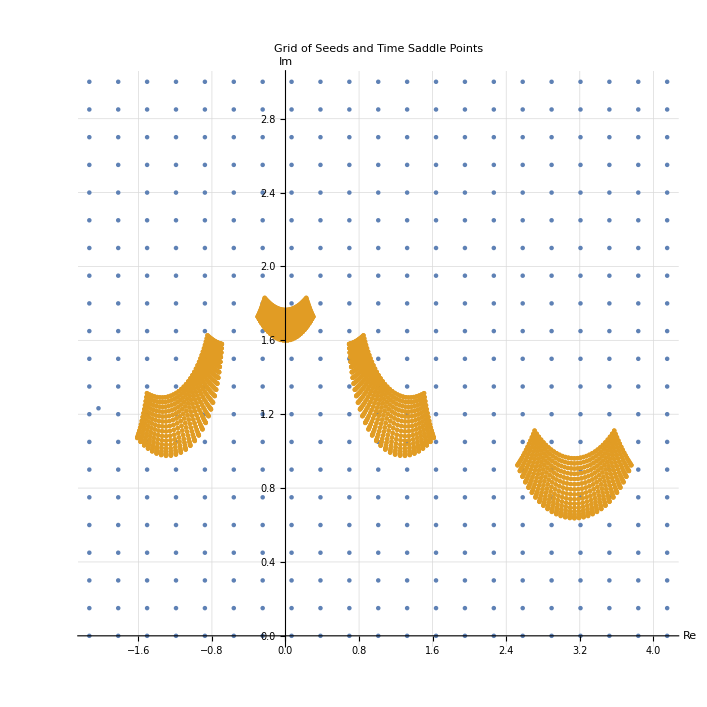

-Graphics3D-

```mathematica
Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
plotRoots=ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large];

Show[plotEx,plotEy,plotRoots,PlotRange->All,PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
(*Extract time,Ex,and Ey values*)
timeValues=Re[#]&/@filteredTValues;
exValues=E1[#][[1]]&/@timeValues;
eyValues=E1[#][[2]]&/@timeValues;
(*Create root points for plotting*)
rootPoints=Graphics3D[{Red,PointSize[Large],Point[Transpose[{exValues,eyValues,timeValues}]]}];
(*Create 3D plot*)
Show[
ParametricPlot3D[{E1[t][[1]],E1[t][[2]],t},{t,-2.133,4.15},
PlotStyle->{Blue},AxesLabel->{"Electric Field Ex","Electric Field Ey","Time, t"},PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]<>", 3D Electric Field Plot",ImageSize->{1200,600},PlotRange->All],
rootPoints,ImageSize->{1200,600}],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

(*Plot the grid of seeds and the time saddle points*)
ListPlot[{seedPoints,realAndImagTimes},AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Grid of Seeds and Time Saddle Points"]

(*Plot the 3D graph with color representing py*)ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"4D Data Representation",ImageSize->Large,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Top}]]
```

# Calculating the Yield

if  the  saddle  point  solutions  generated  by  a  px  py  value  does  not  give  4  solutions  then  indexing  below  does  not  work  properly  as  it  assumes  format  of  time  saddle  points  to  be  ((px, py, ts1, ts2, ts3, ts4), so  on)  for  all  different  combinations  of  different  px  and  py  values .

```mathematica
(*Selects time saddle point solutions for trajectory A,B,C,D individually and accordingly*)
timeA=Table[validData[[i]],{i,1,Length[validData],4}];
timeB=Table[validData[[i]],{i,2,Length[validData],4}];
timeC=Table[validData[[i]],{i,3,Length[validData],4}];
timeD=Table[validData[[i]],{i,4,Length[validData],4}];
Print[Length[timeA]]

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A*)
psiA =Table[
prefactor*action[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}])
],
{i,1,Length[timeA]}];
Print[Length[psiA]]
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj B*)
psiB=Table[
prefactor*action[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}])
],
{i,1,Length[timeB]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiC=Table[
prefactor*action[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}])
],
{i,1,Length[timeC]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiD=Table[
prefactor*action[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}])
],
{i,1,Length[timeD]}];

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A+B+C+D*)
totalPsi =psiA+psiB +psiC +psiD;
```

961

{6.7484×10^-15+4.56303×10^-15 ⅈ,-6.62621×10^-14-2.24259×10^-13 ⅈ,-7.71638×10^-13+5.01747×10^-12 ⅈ,2.81605×10^-11-7.90654×10^-11 ⅈ,-2.94186×10^-10+1.02361×10^-9 ⅈ,-3.78945×10^-10-1.04417×10^-8 ⅈ,4.56493×10^-8+6.55771×10^-8 ⅈ,-4.75706×10^-7-6.34429×10^-8 ⅈ,1.31178×10^-6-1.86762×10^-6 ⅈ,5.85709×10^-6+6.37606×10^-6 ⅈ,-0.0000184775+0.0000188293 ⅈ,-0.0000584484-0.0000284981 ⅈ,-0.0000184787-0.000128997 ⅈ,0.00011268-0.000181189 ⅈ,0.000237303-0.000160392 ⅈ,0.000283906-0.000138625 ⅈ,0.000237303-0.000160392 ⅈ,0.00011268-0.000181189 ⅈ,-0.0000184787-0.000128997 ⅈ,-0.0000584484-0.0000284981 ⅈ,-0.0000184775+0.0000188293 ⅈ,5.85709×10^-6+6.37606×10^-6 ⅈ,1.31178×10^-6-1.86762×10^-6 ⅈ,-4.75706×10^-7-6.34429×10^-8 ⅈ,4.56493×10^-8+6.55771×10^-8 ⅈ,-3.78945×10^-10-1.04417×10^-8 ⅈ,-2.94186×10^-10+1.02361×10^-9 ⅈ,2.81605×10^-11-7.90654×10^-11 ⅈ,-7.71638×10^-13+5.01747×10^-12 ⅈ,-6.62621×10^-14-2.24259×10^-13 ⅈ,6.7484×10^-15+4.56303×10^-15 ⅈ,2.13334×10^-14-2.92796×10^-15 ⅈ,-5.36965×10^-13-2.83089×10^-13 ⅈ,8.43534×10^-12+9.80175×10^-12 ⅈ,-1.15502×10^-10-1.75109×10^-10 ⅈ,1.69006×10^-9+1.989×10^-9 ⅈ,-2.20989×10^-8-1.19338×10^-8 ⅈ,1.86807×10^-7-2.4088×10^-8 ⅈ,-5.94373×10^-7+9.37602×10^-7 ⅈ,-2.7936×10^-6-4.36722×10^-6 ⅈ,0.0000178684-7.37891×10^-6 ⅈ,0.0000265869+0.0000515718 ⅈ,-0.0000956635+0.000103689 ⅈ,-0.000277379-0.0000356275 ⅈ,-0.000312878-0.000329273 ⅈ,-0.000207656-0.000570161 ⅈ,-0.000140721-0.000653012 ⅈ,-0.000207656-0.000570161 ⅈ,-0.000312878-0.000329273 ⅈ,-0.000277379-0.0000356275 ⅈ,-0.0000956635+0.000103689 ⅈ,0.0000265869+0.0000515718 ⅈ,0.0000178684-7.37891×10^-6 ⅈ,-2.7936×10^-6-4.36722×10^-6 ⅈ,-5.94373×10^-7+9.37602×10^-7 ⅈ,1.86807×10^-7-2.4088×10^-8 ⅈ,-2.20989×10^-8-1.19338×10^-8 ⅈ,1.69006×10^-9+1.989×10^-9 ⅈ,-1.15502×10^-10-1.75109×10^-10 ⅈ,8.43534×10^-12+9.80175×10^-12 ⅈ,-5.36965×10^-13-2.83089×10^-13 ⅈ,2.13334×10^-14-2.92796×10^-15 ⅈ,2.02424×10^-14-4.48486×10^-14 ⅈ,-1.1315×10^-12+7.65333×10^-13 ⅈ,2.74769×10^-11-8.108×10^-12 ⅈ,-4.45678×10^-10+1.01442×10^-10 ⅈ,5.13724×10^-9-2.21056×10^-9 ⅈ,-3.54757×10^-8+3.92436×10^-8 ⅈ,2.23605×10^-8-3.8938×10^-7 ⅈ,1.72778×10^-6+1.45762×10^-6 ⅈ,-9.2195×10^-6+4.78319×10^-6 ⅈ,-0.000012772-0.0000359407 ⅈ,0.000101101-0.0000502091 ⅈ,0.000201858+0.000181056 ⅈ,-0.0000482414+0.00052995 ⅈ,-0.000589327+0.000623405 ⅈ,-0.0010448+0.00045768 ⅈ,-0.00120531+0.000345504 ⅈ,-0.0010448+0.00045768 ⅈ,-0.000589327+0.000623405 ⅈ,-0.0000482414+0.00052995 ⅈ,0.000201858+0.000181056 ⅈ,0.000101101-0.0000502091 ⅈ,-0.000012772-0.0000359407 ⅈ,-9.2195×10^-6+4.78319×10^-6 ⅈ,1.72778×10^-6+1.45762×10^-6 ⅈ,2.23605×10^-8-3.8938×10^-7 ⅈ,-3.54757×10^-8+3.92436×10^-8 ⅈ,5.13724×10^-9-2.21056×10^-9 ⅈ,-4.45678×10^-10+1.01442×10^-10 ⅈ,2.74769×10^-11-8.108×10^-12 ⅈ,-1.1315×10^-12+7.65333×10^-13 ⅈ,2.02424×10^-14-4.48486×10^-14 ⅈ,-7.37532×10^-14-6.38707×10^-14 ⅈ,9.84922×10^-13+2.48874×10^-12 ⅈ,-7.64233×10^-12-5.4893×10^-11 ⅈ,1.23389×10^-10+8.63806×10^-10 ⅈ,-3.98614×10^-9-9.74699×10^-9 ⅈ,7.5553×10^-8+6.27246×10^-8 ⅈ,-7.13125×10^-7+2.94374×10^-8 ⅈ,2.12992×10^-6-3.47767×10^-6 ⅈ,0.0000115831+0.0000143954 ⅈ,-0.0000559028+0.0000368698 ⅈ,-0.000131928-0.000144599 ⅈ,0.000190344-0.000424507 ⅈ,0.000878262-0.000218122 ⅈ,0.00133187+0.000571333 ⅈ,0.00134379+0.00136983 ⅈ,0.00126769+0.00168249 ⅈ,0.00134379+0.00136983 ⅈ,0.00133187+0.000571333 ⅈ,0.000878262-0.000218122 ⅈ,0.000190344-0.000424507 ⅈ,-0.000131928-0.000144599 ⅈ,-0.0000559028+0.0000368698 ⅈ,0.0000115831+0.0000143954 ⅈ,2.12992×10^-6-3.47767×10^-6 ⅈ,-7.13125×10^-7+2.94374×10^-8 ⅈ,7.5553×10^-8+6.27246×10^-8 ⅈ,-3.98614×10^-9-9.74699×10^-9 ⅈ,1.23389×10^-10+8.63806×10^-10 ⅈ,-7.64233×10^-12-5.4893×10^-11 ⅈ,9.84922×10^-13+2.48874×10^-12 ⅈ,-7.37532×10^-14-6.38707×10^-14 ⅈ,-1.13698×10^-13+1.2416×10^-13 ⅈ,4.17754×10^-12-1.87755×10^-12 ⅈ,-9.09252×10^-11+2.3726×10^-11 ⅈ,1.38714×10^-9-4.71346×10^-10 ⅈ,-1.4039×10^-8+1.04454×10^-8 ⅈ,5.97029×10^-8-1.49977×10^-7 ⅈ,4.66925×10^-7+1.06205×10^-6 ⅈ,-6.5043×10^-6-7.97711×10^-7 ⅈ,0.0000118543-0.0000268637 ⅈ,0.0000940774+0.0000472275 ⅈ,-0.0000812169+0.000293678 ⅈ,-0.000706991+0.000123409 ⅈ,-0.00105347-0.000899974 ⅈ,-0.000512135-0.00214648 ⅈ,0.000418442-0.00288133 ⅈ,0.00085263-0.00307637 ⅈ,0.000418442-0.00288133 ⅈ,-0.000512135-0.00214648 ⅈ,-0.00105347-0.000899974 ⅈ,-0.000706991+0.000123409 ⅈ,-0.0000812169+0.000293678 ⅈ,0.0000940774+0.0000472275 ⅈ,0.0000118543-0.0000268637 ⅈ,-6.5043×10^-6-7.97711×10^-7 ⅈ,4.66925×10^-7+1.06205×10^-6 ⅈ,5.97029×10^-8-1.49977×10^-7 ⅈ,-1.4039×10^-8+1.04454×10^-8 ⅈ,1.38714×10^-9-4.71346×10^-10 ⅈ,-9.09252×10^-11+2.3726×10^-11 ⅈ,4.17754×10^-12-1.87755×10^-12 ⅈ,-1.13698×10^-13+1.2416×10^-13 ⅈ,2.20371×10^-13+1.25255×10^-13 ⅈ,-4.53559×10^-12-5.15173×10^-12 ⅈ,8.22446×10^-11+1.13394×10^-10 ⅈ,-1.51151×10^-9-1.55844×10^-9 ⅈ,2.35098×10^-8+1.05248×10^-8 ⅈ,-2.31396×10^-7+4.59274×10^-8 ⅈ,8.37505×10^-7-1.45942×10^-6 ⅈ,5.091×10^-6+7.9377×10^-6 ⅈ,-0.0000396709+0.0000135323 ⅈ,-0.0000477319-0.000141256 ⅈ,0.000362347-0.000228314 ⅈ,0.000863777+0.00050787 ⅈ,0.000357722+0.00189012 ⅈ,-0.00125127+0.00278151 ⅈ,-0.00284768+0.00282821 ⅈ,-0.00347405+0.00269531 ⅈ,-0.00284768+0.00282821 ⅈ,-0.00125127+0.00278151 ⅈ,0.000357722+0.00189012 ⅈ,0.000863777+0.00050787 ⅈ,0.000362347-0.000228314 ⅈ,-0.0000477319-0.000141256 ⅈ,-0.0000396709+0.0000135323 ⅈ,5.091×10^-6+7.9377×10^-6 ⅈ,8.37505×10^-7-1.45942×10^-6 ⅈ,-2.31396×10^-7+4.59274×10^-8 ⅈ,2.35098×10^-8+1.05248×10^-8 ⅈ,-1.51151×10^-9-1.55844×10^-9 ⅈ,8.22446×10^-11+1.13394×10^-10 ⅈ,-4.53559×10^-12-5.15173×10^-12 ⅈ,2.20371×10^-13+1.25255×10^-13 ⅈ,-1.65706×10^-14+3.33129×10^-13 ⅈ,2.71758×10^-12-8.60656×10^-12 ⅈ,-5.89743×10^-11+1.74285×10^-10 ⅈ,-3.17772×10^-10+2.82845×10^-9 ⅈ,-1.1138×10^-8-3.17912×10^-8 ⅈ,2.62065×10^-7+1.61029×10^-7 ⅈ,-2.04163×10^-6+7.80685×10^-7 ⅈ,6.80625×10^-7-0.0000121807 ⅈ,0.0000523874+0.0000130276 ⅈ,-0.0000376638+0.000187382 ⅈ,-0.000544772+0.0000440677 ⅈ,-0.000712149-0.00105554 ⅈ,0.000555209-0.00237132 ⅈ,0.00281219-0.00263032 ⅈ,0.00466206-0.00196341 ⅈ,0.00532074-0.00153428 ⅈ,0.00466206-0.00196341 ⅈ,0.00281219-0.00263032 ⅈ,0.000555209-0.00237132 ⅈ,-0.000712149-0.00105554 ⅈ,-0.000544772+0.0000440677 ⅈ,-0.0000376638+0.000187382 ⅈ,0.0000523874+0.0000130276 ⅈ,6.80625×10^-7-0.0000121807 ⅈ,-2.04163×10^-6+7.80685×10^-7 ⅈ,2.62065×10^-7+1.61029×10^-7 ⅈ,-1.1138×10^-8-3.17912×10^-8 ⅈ,-3.17772×10^-10+2.82845×10^-9 ⅈ,-5.89743×10^-11+1.74285×10^-10 ⅈ,2.71758×10^-12-8.60656×10^-12 ⅈ,-1.65706×10^-14+3.33129×10^-13 ⅈ,3.05735×10^-13-2.3226×10^-13 ⅈ,-9.29757×10^-12+4.72561×10^-12 ⅈ,1.84631×10^-10-1.06804×10^-10 ⅈ,-2.27751×10^-9+2.39947×10^-9 ⅈ,9.34069×10^-9-3.80995×10^-8 ⅈ,1.74824×10^-7+3.13106×10^-7 ⅈ,-2.54136×10^-6-2.08002×10^-7 ⅈ,6.10181×10^-6-0.0000128556 ⅈ,0.0000527766+0.0000342845 ⅈ,-0.000103015+0.000197331 ⅈ,0.000627867+0.000100299 ⅈ,0.000564302+0.00136734 ⅈ,-0.00110704+0.00259983 ⅈ,-0.00368049+0.0025242 ⅈ,-0.00565883+0.00151167 ⅈ,-0.00634195+0.000942206 ⅈ,-0.00565883+0.00151167 ⅈ,-0.00368049+0.0025242 ⅈ,-0.00110704+0.00259983 ⅈ,0.000564302+0.00136734 ⅈ,0.000627867+0.000100299 ⅈ,-0.000103015+0.000197331 ⅈ,0.0000527766+0.0000342845 ⅈ,6.10181×10^-6-0.0000128556 ⅈ,-2.54136×10^-6-2.08002×10^-7 ⅈ,1.74824×10^-7+3.13106×10^-7 ⅈ,9.34069×10^-9-3.80995×10^-8 ⅈ,-2.27751×10^-9+2.39947×10^-9 ⅈ,1.84631×10^-10-1.06804×10^-10 ⅈ,-9.29757×10^-12+4.72561×10^-12 ⅈ,3.05735×10^-13-2.3226×10^-13 ⅈ,-3.86771×10^-13+1.01394×10^-16 ⅈ,1.05374×10^-11+1.08257×10^-12 ⅈ,-2.18219×10^-10+5.85126×10^-12 ⅈ,3.15838×10^-9-1.2862×10^-9 ⅈ,-2.28021×10^-8+3.37049×10^-8 ⅈ,-8.25347×10^-8-3.65017×10^-7 ⅈ,2.55142×10^-6+8.01282×10^-7 ⅈ,-8.5367×10^-6+0.0000123261 ⅈ,-0.0000516235-0.0000420014 ⅈ,0.000120912-0.000202809 ⅈ,0.000666104+0.000114679 ⅈ,0.000638094+0.0014402 ⅈ,-0.0010232+0.00283336 ⅈ,-0.00370501+0.00299098 ⅈ,-0.00586803+0.00215917 ⅈ,-0.00664258+0.00165121 ⅈ,-0.00586803+0.00215917 ⅈ,-0.00370501+0.00299098 ⅈ,-0.0010232+0.00283336 ⅈ,0.000638094+0.0014402 ⅈ,0.000666104+0.000114679 ⅈ,0.000120912-0.000202809 ⅈ,-0.0000516235-0.0000420014 ⅈ,-8.5367×10^-6+0.0000123261 ⅈ,2.55142×10^-6+8.01282×10^-7 ⅈ,-8.25347×10^-8-3.65017×10^-7 ⅈ,-2.28021×10^-8+3.37049×10^-8 ⅈ,3.15838×10^-9-1.2862×10^-9 ⅈ,-2.18219×10^-10+5.85126×10^-12 ⅈ,1.05374×10^-11+1.08257×10^-12 ⅈ,-3.86771×10^-13+1.01394×10^-16 ⅈ,3.08595×10^-13+1.44533×10^-13 ⅈ,-8.45337×10^-12-4.23157×10^-12 ⅈ,1.90569×10^-10+5.06937×10^-11 ⅈ,-3.07061×10^-9+5.3481×10^-10 ⅈ,2.53277×10^-8-2.7807×10^-8 ⅈ,5.07914×10^-8+3.45802×10^-7 ⅈ,-2.39724×10^-6-7.85596×10^-7 ⅈ,7.55454×10^-6-0.0000121045 ⅈ,0.00005343+0.0000349655 ⅈ,-0.0000853596+0.00021161 ⅈ,-0.000656934+0.0000185784 ⅈ,-0.000935961-0.00122177 ⅈ,0.000234853-0.00294604 ⅈ,0.00265371-0.0038611 ⅈ,0.00488493-0.00375679 ⅈ,0.00574951-0.00353557 ⅈ,0.00488493-0.00375679 ⅈ,0.00265371-0.0038611 ⅈ,0.000234853-0.00294604 ⅈ,-0.000935961-0.00122177 ⅈ,-0.000656934+0.0000185784 ⅈ,-0.0000853596+0.00021161 ⅈ,0.00005343+0.0000349655 ⅈ,7.55454×10^-6-0.0000121045 ⅈ,-2.39724×10^-6-7.85596×10^-7 ⅈ,5.07914×10^-8+3.45802×10^-7 ⅈ,2.53277×10^-8-2.7807×10^-8 ⅈ,-3.07061×10^-9+5.3481×10^-10 ⅈ,1.90569×10^-10+5.06937×10^-11 ⅈ,-8.45337×10^-12-4.23157×10^-12 ⅈ,3.08595×10^-13+1.44533×10^-13 ⅈ,-2.04557×10^-13-1.63925×10^-13 ⅈ,5.99637×10^-12+4.33336×10^-12 ⅈ,-1.47566×10^-10-5.35104×10^-11 ⅈ,2.49091×10^-9-3.93393×10^-10 ⅈ,-1.95673×10^-8+2.39395×10^-8 ⅈ,-7.6783×10^-8-2.8147×10^-7 ⅈ,2.11734×10^-6+2.83267×10^-7 ⅈ,-3.78931×10^-6+0.0000116486 ⅈ,-0.0000533339-0.0000153851 ⅈ,6.97581×10^-6-0.000200483 ⅈ,0.000532611-0.000238561 ⅈ,0.00121847+0.000644605 ⅈ,0.000991246+0.00247391 ⅈ,-0.000505584+0.00421537 ⅈ,-0.00227871+0.00511677 ⅈ,-0.00304381+0.0053339 ⅈ,-0.00227871+0.00511677 ⅈ,-0.000505584+0.00421537 ⅈ,0.000991246+0.00247391 ⅈ,0.00121847+0.000644605 ⅈ,0.000532611-0.000238561 ⅈ,6.97581×10^-6-0.000200483 ⅈ,-0.0000533339-0.0000153851 ⅈ,-3.78931×10^-6+0.0000116486 ⅈ,2.11734×10^-6+2.83267×10^-7 ⅈ,-7.6783×10^-8-2.8147×10^-7 ⅈ,-1.95673×10^-8+2.39395×10^-8 ⅈ,2.49091×10^-9-3.93393×10^-10 ⅈ,-1.47566×10^-10-5.35104×10^-11 ⅈ,5.99637×10^-12+4.33336×10^-12 ⅈ,-2.04557×10^-13-1.63925×10^-13 ⅈ,1.31778×10^-13+1.16185×10^-13 ⅈ,-4.185×10^-12-2.85411×10^-12 ⅈ,1.0644×10^-10+2.69401×10^-11 ⅈ,-1.70603×10^-9+5.78873×10^-10 ⅈ,9.73546×10^-9-2.03351×10^-8 ⅈ,1.17151×10^-7+1.82653×10^-7 ⅈ,-1.57577×10^-6+3.74274×10^-7 ⅈ,-1.03672×10^-6-9.40039×10^-6 ⅈ,0.0000427392-8.55318×10^-6 ⅈ,0.0000756423+0.000140999 ⅈ,-0.000258332+0.000394909 ⅈ,-0.00111986+0.000135585 ⅈ,-0.00187308-0.00115655 ⅈ,-0.00181178-0.00303123 ⅈ,-0.00116861-0.00453099 ⅈ,-0.000804232-0.00507442 ⅈ,-0.00116861-0.00453099 ⅈ,-0.00181178-0.00303123 ⅈ,-0.00187308-0.00115655 ⅈ,-0.00111986+0.000135585 ⅈ,-0.000258332+0.000394909 ⅈ,0.0000756423+0.000140999 ⅈ,0.0000427392-8.55318×10^-6 ⅈ,-1.03672×10^-6-9.40039×10^-6 ⅈ,-1.57577×10^-6+3.74274×10^-7 ⅈ,1.17151×10^-7+1.82653×10^-7 ⅈ,9.73546×10^-9-2.03351×10^-8 ⅈ,-1.70603×10^-9+5.78873×10^-10 ⅈ,1.0644×10^-10+2.69401×10^-11 ⅈ,-4.185×10^-12-2.85411×10^-12 ⅈ,1.31778×10^-13+1.16185×10^-13 ⅈ,-8.49523×10^-14-5.6865×10^-14 ⅈ,2.7941×10^-12+1.15842×10^-12 ⅈ,-6.72353×10^-11+1.90657×10^-12 ⅈ,8.85664×10^-10-7.04747×10^-10 ⅈ,-5.13071×10^-10+1.45132×10^-8 ⅈ,-1.23853×10^-7-7.18808×10^-8 ⅈ,7.87269×10^-7-7.60125×10^-7 ⅈ,4.21473×10^-6+4.99365×10^-6 ⅈ,-0.0000205175+0.0000229169 ⅈ,-0.000106567-0.0000435624 ⅈ,-0.000052476-0.000341536 ⅈ,0.000529426-0.000650149 ⅈ,0.00160807-0.000397065 ⅈ,0.00261914+0.000574921 ⅈ,0.00315254+0.00168069 ⅈ,0.00328565+0.00215671 ⅈ,0.00315254+0.00168069 ⅈ,0.00261914+0.000574921 ⅈ,0.00160807-0.000397065 ⅈ,0.000529426-0.000650149 ⅈ,-0.000052476-0.000341536 ⅈ,-0.000106567-0.0000435624 ⅈ,-0.0000205175+0.0000229169 ⅈ,4.21473×10^-6+4.99365×10^-6 ⅈ,7.87269×10^-7-7.60125×10^-7 ⅈ,-1.23853×10^-7-7.18808×10^-8 ⅈ,-5.13071×10^-10+1.45132×10^-8 ⅈ,8.85664×10^-10-7.04747×10^-10 ⅈ,-6.72353×10^-11+1.90657×10^-12 ⅈ,2.7941×10^-12+1.15842×10^-12 ⅈ,-8.49523×10^-14-5.6865×10^-14 ⅈ,4.93388×10^-14+1.45401×10^-14 ⅈ,-1.56759×10^-12-3.06767×10^-14 ⅈ,3.20104×10^-11-1.62748×10^-11 ⅈ,-2.36751×10^-10+5.75392×10^-10 ⅈ,-4.20366×10^-9-7.06315×10^-9 ⅈ,8.29101×10^-8-8.90664×10^-9 ⅈ,-7.34556×10^-8+6.50836×10^-7 ⅈ,-3.98419×10^-6-5.02162×10^-7 ⅈ,-1.23161×10^-6-0.0000193401 ⅈ,0.0000668142-0.0000323125 ⅈ,0.000194997+0.00011706 ⅈ,0.000126735+0.000547363 ⅈ,-0.000429449+0.0010413 ⅈ,-0.00135973+0.00124411 ⅈ,-0.00219367+0.00113928 ⅈ,-0.00251865+0.00104095 ⅈ,-0.00219367+0.00113928 ⅈ,-0.00135973+0.00124411 ⅈ,-0.000429449+0.0010413 ⅈ,0.000126735+0.000547363 ⅈ,0.000194997+0.00011706 ⅈ,0.0000668142-0.0000323125 ⅈ,-1.23161×10^-6-0.0000193401 ⅈ,-3.98419×10^-6-5.02162×10^-7 ⅈ,-7.34556×10^-8+6.50836×10^-7 ⅈ,8.29101×10^-8-8.90664×10^-9 ⅈ,-4.20366×10^-9-7.06315×10^-9 ⅈ,-2.36751×10^-10+5.75392×10^-10 ⅈ,3.20104×10^-11-1.62748×10^-11 ⅈ,-1.56759×10^-12-3.06767×10^-14 ⅈ,4.93388×10^-14+1.45401×10^-14 ⅈ,-2.19228×10^-14+3.93186×10^-15 ⅈ,6.11771×10^-13-3.44105×10^-13 ⅈ,-8.00731×10^-12+1.45631×10^-11 ⅈ,-7.95616×10^-11-2.86812×10^-10 ⅈ,3.86514×10^-9+1.24734×10^-9 ⅈ,-2.68887×10^-8+3.29769×10^-8 ⅈ,-2.27788×10^-7-2.58787×10^-7 ⅈ,1.57935×10^-6-1.49978×10^-6 ⅈ,9.0685×10^-6+5.88649×10^-6 ⅈ,-6.23165×10^-6+0.0000420423 ⅈ,-0.000118927+0.0000603066 ⅈ,-0.000320872-0.000100174 ⅈ,-0.000427596-0.000535318 ⅈ,-0.000284261-0.00109879 ⅈ,-3.23993×10^-6-0.00153396 ⅈ,0.000137514-0.00168984 ⅈ,-3.23993×10^-6-0.00153396 ⅈ,-0.000284261-0.00109879 ⅈ,-0.000427596-0.000535318 ⅈ,-0.000320872-0.000100174 ⅈ,-0.000118927+0.0000603066 ⅈ,-6.23165×10^-6+0.0000420423 ⅈ,9.0685×10^-6+5.88649×10^-6 ⅈ,1.57935×10^-6-1.49978×10^-6 ⅈ,-2.27788×10^-7-2.58787×10^-7 ⅈ,-2.68887×10^-8+3.29769×10^-8 ⅈ,3.86514×10^-9+1.24734×10^-9 ⅈ,-7.95616×10^-11-2.86812×10^-10 ⅈ,-8.00731×10^-12+1.45631×10^-11 ⅈ,6.11771×10^-13-3.44105×10^-13 ⅈ,-2.19228×10^-14+3.93186×10^-15 ⅈ,5.78812×10^-15-5.88496×10^-15 ⅈ,-9.9412×10^-14+2.50785×10^-13 ⅈ,-1.57996×10^-12-6.43266×10^-12 ⅈ,1.08189×10^-10+5.85835×10^-11 ⅈ,-1.48423×10^-9+9.08394×10^-10 ⅈ,-4.33938×10^-9-1.83731×10^-8 ⅈ,1.5719×10^-7-1.86246×10^-8 ⅈ,2.08293×10^-7+1.01188×10^-6 ⅈ,-4.68845×10^-6+2.4516×10^-6 ⅈ,-0.0000173945-0.0000124687 ⅈ,-1.92733×10^-6-0.000068859 ⅈ,0.0001165-0.000134015 ⅈ,0.000353891-0.000102977 ⅈ,0.000614133+0.0000750149 ⅈ,0.000788331+0.000299212 ⅈ,0.000844301+0.000400549 ⅈ,0.000788331+0.000299212 ⅈ,0.000614133+0.0000750149 ⅈ,0.000353891-0.000102977 ⅈ,0.0001165-0.000134015 ⅈ,-1.92733×10^-6-0.000068859 ⅈ,-0.0000173945-0.0000124687 ⅈ,-4.68845×10^-6+2.4516×10^-6 ⅈ,2.08293×10^-7+1.01188×10^-6 ⅈ,1.5719×10^-7-1.86246×10^-8 ⅈ,-4.33938×10^-9-1.83731×10^-8 ⅈ,-1.48423×10^-9+9.08394×10^-10 ⅈ,1.08189×10^-10+5.85835×10^-11 ⅈ,-1.57996×10^-12-6.43266×10^-12 ⅈ,-9.9412×10^-14+2.50785×10^-13 ⅈ,5.78812×10^-15-5.88496×10^-15 ⅈ,-4.35009×10^-17+2.60106×10^-15 ⅈ,-3.80283×10^-14-7.98379×10^-14 ⅈ,2.03513×10^-12+9.79632×10^-13 ⅈ,-3.94238×10^-11+1.86463×10^-11 ⅈ,1.89824×10^-11-6.40776×10^-10 ⅈ,6.90658×10^-9+2.10768×10^-9 ⅈ,-2.22783×10^-8+5.87151×10^-8 ⅈ,-4.13009×10^-7-9.8414×10^-8 ⅈ,-1.89427×10^-7-2.23918×10^-6 ⅈ,7.80462×10^-6-5.18858×10^-6 ⅈ,0.0000295822+9.27679×10^-6 ⅈ,0.0000426438+0.0000698259 ⅈ,-6.41312×10^-7+0.000173114 ⅈ,-0.000113151+0.00027219 ⅈ,-0.000237637+0.000328187 ⅈ,-0.000291468+0.000343422 ⅈ,-0.000237637+0.000328187 ⅈ,-0.000113151+0.00027219 ⅈ,-6.41312×10^-7+0.000173114 ⅈ,0.0000426438+0.0000698259 ⅈ,0.0000295822+9.27679×10^-6 ⅈ,7.80462×10^-6-5.18858×10^-6 ⅈ,-1.89427×10^-7-2.23918×10^-6 ⅈ,-4.13009×10^-7-9.8414×10^-8 ⅈ,-2.22783×10^-8+5.87151×10^-8 ⅈ,6.90658×10^-9+2.10768×10^-9 ⅈ,1.89824×10^-11-6.40776×10^-10 ⅈ,-3.94238×10^-11+1.86463×10^-11 ⅈ,2.03513×10^-12+9.79632×10^-13 ⅈ,-3.80283×10^-14-7.98379×10^-14 ⅈ,-4.35009×10^-17+2.60106×10^-15 ⅈ,-5.33986×10^-16-4.41323×10^-16 ⅈ,2.41952×10^-14+4.18174×10^-15 ⅈ,-5.53007×10^-13+3.48498×10^-13 ⅈ,8.54024×10^-13-1.31262×10^-11 ⅈ,1.78021×10^-10+9.40647×10^-11 ⅈ,-1.53027×10^-9+1.79662×10^-9 ⅈ,-1.5919×10^-8-1.41971×10^-8 ⅈ,7.94329×10^-8-1.26754×10^-7 ⅈ,8.02222×10^-7+1.67308×10^-7 ⅈ,1.13718×10^-6+3.33967×10^-6 ⅈ,-6.12539×10^-6+0.0000103274 ⅈ,-0.0000306189+0.000010811 ⅈ,-0.0000687435-0.0000135816 ⅈ,-0.000101737-0.0000656341 ⅈ,-0.000117245-0.000120201 ⅈ,-0.000120387-0.000143447 ⅈ,-0.000117245-0.000120201 ⅈ,-0.000101737-0.0000656341 ⅈ,-0.0000687435-0.0000135816 ⅈ,-0.0000306189+0.000010811 ⅈ,-6.12539×10^-6+0.0000103274 ⅈ,1.13718×10^-6+3.33967×10^-6 ⅈ,8.02222×10^-7+1.67308×10^-7 ⅈ,7.94329×10^-8-1.26754×10^-7 ⅈ,-1.5919×10^-8-1.41971×10^-8 ⅈ,-1.53027×10^-9+1.79662×10^-9 ⅈ,1.78021×10^-10+9.40647×10^-11 ⅈ,8.54024×10^-13-1.31262×10^-11 ⅈ,-5.53007×10^-13+3.48498×10^-13 ⅈ,2.41952×10^-14+4.18174×10^-15 ⅈ,-5.33986×10^-16-4.41323×10^-16 ⅈ,1.46147×10^-16-5.11033×10^-17 ⅈ,-3.51449×10^-15+4.5277×10^-15 ⅈ,-1.99187×10^-14-1.5811×10^-13 ⅈ,3.01036×10^-12+1.4633×10^-12 ⅈ,-3.9331×10^-11+3.61881×10^-11 ⅈ,-3.50853×10^-10-5.50467×10^-10 ⅈ,5.1187×10^-9-3.38686×10^-9 ⅈ,3.17367×10^-8+3.14919×10^-8 ⅈ,-9.7655×10^-8+2.34177×10^-7 ⅈ,-1.11291×10^-6+1.87579×10^-7 ⅈ,-3.0923×10^-6-2.46328×10^-6 ⅈ,-2.41109×10^-6-0.0000106904 ⅈ,7.07049×10^-6-0.0000230676 ⅈ,0.0000260816-0.000033313 ⅈ,0.0000457405-0.0000375938 ⅈ,0.0000540658-0.0000382282 ⅈ,0.0000457405-0.0000375938 ⅈ,0.0000260816-0.000033313 ⅈ,7.07049×10^-6-0.0000230676 ⅈ,-2.41109×10^-6-0.0000106904 ⅈ,-3.0923×10^-6-2.46328×10^-6 ⅈ,-1.11291×10^-6+1.87579×10^-7 ⅈ,-9.7655×10^-8+2.34177×10^-7 ⅈ,3.17367×10^-8+3.14919×10^-8 ⅈ,5.1187×10^-9-3.38686×10^-9 ⅈ,-3.50853×10^-10-5.50467×10^-10 ⅈ,-3.9331×10^-11+3.61881×10^-11 ⅈ,3.01036×10^-12+1.4633×10^-12 ⅈ,-1.99187×10^-14-1.5811×10^-13 ⅈ,-3.51449×10^-15+4.5277×10^-15 ⅈ,1.46147×10^-16-5.11033×10^-17 ⅈ,-2.39399×10^-18+2.87307×10^-17 ⅈ,-5.76222×10^-16-9.56415×10^-16 ⅈ,3.18552×10^-14+6.26976×10^-15 ⅈ,-4.73354×10^-13+5.32748×10^-13 ⅈ,-5.82561×10^-12-1.03561×10^-11 ⅈ,1.40813×10^-10-5.55232×10^-11 ⅈ,6.16258×10^-10+1.34808×10^-9 ⅈ,-8.81965×10^-9+6.93144×10^-9 ⅈ,-5.82364×10^-8-3.10194×10^-8 ⅈ,-2.95299×10^-8-3.01755×10^-7 ⅈ,7.2186×10^-7-8.21286×10^-7 ⅈ,3.05039×10^-6-5.88444×10^-7 ⅈ,6.6323×10^-6+2.16479×10^-6 ⅈ,9.70757×10^-6+7.7376×10^-6 ⅈ,0.0000110903+0.0000135718 ⅈ,0.0000113342+0.000016065 ⅈ,0.0000110903+0.0000135718 ⅈ,9.70757×10^-6+7.7376×10^-6 ⅈ,6.6323×10^-6+2.16479×10^-6 ⅈ,3.05039×10^-6-5.88444×10^-7 ⅈ,7.2186×10^-7-8.21286×10^-7 ⅈ,-2.95299×10^-8-3.01755×10^-7 ⅈ,-5.82364×10^-8-3.10194×10^-8 ⅈ,-8.81965×10^-9+6.93144×10^-9 ⅈ,6.16258×10^-10+1.34808×10^-9 ⅈ,1.40813×10^-10-5.55232×10^-11 ⅈ,-5.82561×10^-12-1.03561×10^-11 ⅈ,-4.73354×10^-13+5.32748×10^-13 ⅈ,3.18552×10^-14+6.26976×10^-15 ⅈ,-5.76222×10^-16-9.56415×10^-16 ⅈ,-2.39399×10^-18+2.87307×10^-17 ⅈ,-4.1176×10^-18-1.66283×10^-18 ⅈ,1.72653×10^-16-5.13899×10^-17 ⅈ,-2.14703×10^-15+5.04446×10^-15 ⅈ,-7.90043×10^-14-9.7996×10^-14 ⅈ,2.03194×10^-12-8.24856×10^-13 ⅈ,8.19458×10^-12+2.79725×10^-11 ⅈ,-2.77095×10^-10+1.07649×10^-10 ⅈ,-1.39064×10^-9-1.87962×10^-9 ⅈ,6.74533×10^-9-1.25573×10^-8 ⅈ,6.7203×10^-8-7.83374×10^-9 ⅈ,1.94637×10^-7+1.58661×10^-7 ⅈ,1.75379×10^-7+7.09782×10^-7 ⅈ,-4.17629×10^-7+1.62115×10^-6 ⅈ,-1.71011×10^-6+2.49121×10^-6 ⅈ,-3.116×10^-6+2.9686×10^-6 ⅈ,-3.72853×10^-6+3.0904×10^-6 ⅈ,-3.116×10^-6+2.9686×10^-6 ⅈ,-1.71011×10^-6+2.49121×10^-6 ⅈ,-4.17629×10^-7+1.62115×10^-6 ⅈ,1.75379×10^-7+7.09782×10^-7 ⅈ,1.94637×10^-7+1.58661×10^-7 ⅈ,6.7203×10^-8-7.83374×10^-9 ⅈ,6.74533×10^-9-1.25573×10^-8 ⅈ,-1.39064×10^-9-1.87962×10^-9 ⅈ,-2.77095×10^-10+1.07649×10^-10 ⅈ,8.19458×10^-12+2.79725×10^-11 ⅈ,2.03194×10^-12-8.24856×10^-13 ⅈ,-7.90043×10^-14-9.7996×10^-14 ⅈ,-2.14703×10^-15+5.04446×10^-15 ⅈ,1.72653×10^-16-5.13899×10^-17 ⅈ,-4.1176×10^-18-1.66283×10^-18 ⅈ,3.03016×10^-19-4.72912×10^-19 ⅈ,3.51003×10^-18+2.36208×10^-17 ⅈ,-6.67037×10^-16-3.66633×10^-16 ⅈ,1.49153×10^-14-1.05795×10^-14 ⅈ,1.17229×10^-13+3.11643×10^-13 ⅈ,-4.42391×10^-12+1.32688×10^-12 ⅈ,-1.93992×10^-11-4.50614×10^-11 ⅈ,3.06897×10^-10-2.57949×10^-10 ⅈ,2.3239×10^-9+1.00572×10^-9 ⅈ,2.70661×10^-9+1.2112×10^-8 ⅈ,-2.53249×10^-8+4.00398×10^-8 ⅈ,-1.31436×10^-7+5.17468×10^-8 ⅈ,-3.27696×10^-7-3.60527×10^-8 ⅈ,-5.42705×10^-7-2.63605×10^-7 ⅈ,-6.86719×10^-7-5.28846×10^-7 ⅈ,-7.32618×10^-7-6.47577×10^-7 ⅈ,-6.86719×10^-7-5.28846×10^-7 ⅈ,-5.42705×10^-7-2.63605×10^-7 ⅈ,-3.27696×10^-7-3.60527×10^-8 ⅈ,-1.31436×10^-7+5.17468×10^-8 ⅈ,-2.53249×10^-8+4.00398×10^-8 ⅈ,2.70661×10^-9+1.2112×10^-8 ⅈ,2.3239×10^-9+1.00572×10^-9 ⅈ,3.06897×10^-10-2.57949×10^-10 ⅈ,-1.93992×10^-11-4.50614×10^-11 ⅈ,-4.42391×10^-12+1.32688×10^-12 ⅈ,1.17229×10^-13+3.11643×10^-13 ⅈ,1.49153×10^-14-1.05795×10^-14 ⅈ,-6.67037×10^-16-3.66633×10^-16 ⅈ,3.51003×10^-18+2.36208×10^-17 ⅈ,3.03016×10^-19-4.72912×10^-19 ⅈ,4.62724×10^-20+3.48388×10^-20 ⅈ,-2.56513×10^-18+2.91315×10^-19 ⅈ,4.12473×10^-17-7.57098×10^-17 ⅈ,1.32259×10^-15+1.71788×10^-15 ⅈ,-3.74715×10^-14+1.72449×10^-14 ⅈ,-2.2837×10^-13-5.51477×10^-13 ⅈ,5.68199×10^-12-3.35905×10^-12 ⅈ,4.2056×10^-11+3.69902×10^-11 ⅈ,-8.63243×10^-11+3.55956×10^-10 ⅈ,-1.70096×10^-9+7.33916×10^-10 ⅈ,-6.79431×10^-9-2.57927×10^-9 ⅈ,-1.229×10^-8-1.8457×10^-8 ⅈ,-5.849×10^-9-5.24035×10^-8 ⅈ,2.18632×10^-8-9.53097×10^-8 ⅈ,5.85358×10^-8-1.2898×10^-7 ⅈ,7.57835×10^-8-1.41195×10^-7 ⅈ,5.85358×10^-8-1.2898×10^-7 ⅈ,2.18632×10^-8-9.53097×10^-8 ⅈ,-5.849×10^-9-5.24035×10^-8 ⅈ,-1.229×10^-8-1.8457×10^-8 ⅈ,-6.79431×10^-9-2.57927×10^-9 ⅈ,-1.70096×10^-9+7.33916×10^-10 ⅈ,-8.63243×10^-11+3.55956×10^-10 ⅈ,4.2056×10^-11+3.69902×10^-11 ⅈ,5.68199×10^-12-3.35905×10^-12 ⅈ,-2.2837×10^-13-5.51477×10^-13 ⅈ,-3.74715×10^-14+1.72449×10^-14 ⅈ,1.32259×10^-15+1.71788×10^-15 ⅈ,4.12473×10^-17-7.57098×10^-17 ⅈ,-2.56513×10^-18+2.91315×10^-19 ⅈ,4.62724×10^-20+3.48388×10^-20 ⅈ,-2.78291×10^-21+3.95459×10^-21 ⅈ,-4.11443×10^-20-2.22227×10^-19 ⅈ,7.30102×10^-18+3.0328×10^-18 ⅈ,-1.45879×10^-16+1.48236×10^-16 ⅈ,-2.32859×10^-15-3.41669×10^-15 ⅈ,5.19849×10^-14-3.44935×10^-14 ⅈ,4.89536×10^-13+5.24767×10^-13 ⅈ,-2.94071×10^-12+5.59325×10^-12 ⅈ,-4.27541×10^-11+7.31496×10^-13 ⅈ,-1.39666×10^-10-1.73754×10^-10 ⅈ,7.25029×10^-11-8.95349×10^-10 ⅈ,1.78839×10^-9-2.15852×10^-9 ⅈ,6.22188×10^-9-2.70307×10^-9 ⅈ,1.2705×10^-8-9.94295×10^-10 ⅈ,1.84691×10^-8+2.21554×10^-9 ⅈ,2.07425×10^-8+3.88376×10^-9 ⅈ,1.84691×10^-8+2.21554×10^-9 ⅈ,1.2705×10^-8-9.94295×10^-10 ⅈ,6.22188×10^-9-2.70307×10^-9 ⅈ,1.78839×10^-9-2.15852×10^-9 ⅈ,7.25029×10^-11-8.95349×10^-10 ⅈ,-1.39666×10^-10-1.73754×10^-10 ⅈ,-4.27541×10^-11+7.31496×10^-13 ⅈ,-2.94071×10^-12+5.59325×10^-12 ⅈ,4.89536×10^-13+5.24767×10^-13 ⅈ,5.19849×10^-14-3.44935×10^-14 ⅈ,-2.32859×10^-15-3.41669×10^-15 ⅈ,-1.45879×10^-16+1.48236×10^-16 ⅈ,7.30102×10^-18+3.0328×10^-18 ⅈ,-4.11443×10^-20-2.22227×10^-19 ⅈ,-2.78291×10^-21+3.95459×10^-21 ⅈ,-2.88416×10^-22-1.48788×10^-22 ⅈ,1.49123×10^-20-5.52312×10^-21 ⅈ,-1.0988×10^-19+5.72061×10^-19 ⅈ,-1.37172×10^-17-8.29406×10^-18 ⅈ,2.17453×10^-16-2.51779×10^-16 ⅈ,3.99793×10^-15+3.3738×10^-15 ⅈ,-3.08137×10^-14+5.44445×10^-14 ⅈ,-5.63782×10^-13-9.14426×10^-14 ⅈ,-1.39142×10^-12-3.74397×10^-12 ⅈ,1.1065×10^-11-1.83768×10^-11 ⅈ,8.51886×10^-11-2.46115×10^-11 ⅈ,2.68245×10^-10+8.92792×10^-11 ⅈ,4.92621×10^-10+4.91566×10^-10 ⅈ,5.86698×10^-10+1.18683×10^-9 ⅈ,5.08015×10^-10+1.87943×10^-9 ⅈ,4.38211×10^-10+2.16986×10^-9 ⅈ,5.08015×10^-10+1.87943×10^-9 ⅈ,5.86698×10^-10+1.18683×10^-9 ⅈ,4.92621×10^-10+4.91566×10^-10 ⅈ,2.68245×10^-10+8.92792×10^-11 ⅈ,8.51886×10^-11-2.46115×10^-11 ⅈ,1.1065×10^-11-1.83768×10^-11 ⅈ,-1.39142×10^-12-3.74397×10^-12 ⅈ,-5.63782×10^-13-9.14426×10^-14 ⅈ,-3.08137×10^-14+5.44445×10^-14 ⅈ,3.99793×10^-15+3.3738×10^-15 ⅈ,2.17453×10^-16-2.51779×10^-16 ⅈ,-1.37172×10^-17-8.29406×10^-18 ⅈ,-1.0988×10^-19+5.72061×10^-19 ⅈ,1.49123×10^-20-5.52312×10^-21 ⅈ,-2.88416×10^-22-1.48788×10^-22 ⅈ,4.08318×10^-24-1.69092×10^-23 ⅈ,5.2354×10^-22+7.23736×10^-22 ⅈ,-3.40445×10^-20+3.79913×10^-21 ⅈ,2.10944×10^-19-9.62278×10^-19 ⅈ,1.99645×10^-17+7.5188×10^-18 ⅈ,-1.12285×10^-16+3.30664×10^-16 ⅈ,-4.30512×10^-15-5.309×10^-16 ⅈ,-1.00559×10^-14-3.97637×10^-14 ⅈ,2.1097×10^-13-2.07881×10^-13 ⅈ,1.62681×10^-12+1.77064×10^-13 ⅈ,4.59395×10^-12+5.1955×10^-12 ⅈ,2.89424×10^-12+2.23858×10^-11 ⅈ,-1.82559×10^-11+5.34568×10^-11 ⅈ,-6.60571×10^-11+8.63939×10^-11 ⅈ,-1.20566×10^-10+1.06819×10^-10 ⅈ,-1.44911×10^-10+1.12692×10^-10 ⅈ,-1.20566×10^-10+1.06819×10^-10 ⅈ,-6.60571×10^-11+8.63939×10^-11 ⅈ,-1.82559×10^-11+5.34568×10^-11 ⅈ,2.89424×10^-12+2.23858×10^-11 ⅈ,4.59395×10^-12+5.1955×10^-12 ⅈ,1.62681×10^-12+1.77064×10^-13 ⅈ,2.1097×10^-13-2.07881×10^-13 ⅈ,-1.00559×10^-14-3.97637×10^-14 ⅈ,-4.30512×10^-15-5.309×10^-16 ⅈ,-1.12285×10^-16+3.30664×10^-16 ⅈ,1.99645×10^-17+7.5188×10^-18 ⅈ,2.10944×10^-19-9.62278×10^-19 ⅈ,-3.40445×10^-20+3.79913×10^-21 ⅈ,5.2354×10^-22+7.23736×10^-22 ⅈ,4.08318×10^-24-1.69092×10^-23 ⅈ,7.35939×10^-25-7.61821×10^-26 ⅈ,-2.16386×10^-23+3.34017×10^-23 ⅈ,-7.76639×10^-22-1.39498×10^-21 ⅈ,4.69417×10^-20-9.7815×10^-21 ⅈ,8.94553×10^-20+1.07875×10^-18 ⅈ,-1.82641×10^-17+2.48462×10^-18 ⅈ,-8.28867×10^-17-2.22624×10^-16 ⅈ,1.71441×10^-15-1.56952×10^-15 ⅈ,1.66031×10^-14+4.89907×10^-15 ⅈ,3.89371×10^-14+9.02719×10^-14 ⅈ,-1.35487×10^-13+4.04682×10^-13 ⅈ,-1.12056×10^-12+8.66885×10^-13 ⅈ,-3.52584×10^-12+7.34197×10^-13 ⅈ,-6.96484×10^-12-8.05796×10^-13 ⅈ,-9.9705×10^-12-3.15241×10^-12 ⅈ,-1.11375×10^-11-4.3182×10^-12 ⅈ,-9.9705×10^-12-3.15241×10^-12 ⅈ,-6.96484×10^-12-8.05796×10^-13 ⅈ,-3.52584×10^-12+7.34197×10^-13 ⅈ,-1.12056×10^-12+8.66885×10^-13 ⅈ,-1.35487×10^-13+4.04682×10^-13 ⅈ,3.89371×10^-14+9.02719×10^-14 ⅈ,1.66031×10^-14+4.89907×10^-15 ⅈ,1.71441×10^-15-1.56952×10^-15 ⅈ,-8.28867×10^-17-2.22624×10^-16 ⅈ,-1.82641×10^-17+2.48462×10^-18 ⅈ,8.94553×10^-20+1.07875×10^-18 ⅈ,4.69417×10^-20-9.7815×10^-21 ⅈ,-7.76639×10^-22-1.39498×10^-21 ⅈ,-2.16386×10^-23+3.34017×10^-23 ⅈ,7.35939×10^-25-7.61821×10^-26 ⅈ,1.28178×10^-26+2.125×10^-26 ⅈ,-1.38919×10^-24-1.5082×10^-25 ⅈ,3.16735×10^-23-4.92843×10^-23 ⅈ,1.20986×10^-21+1.38178×10^-21 ⅈ,-3.52251×10^-20+2.49558×10^-20 ⅈ,-4.83882×10^-19-5.91173×10^-19 ⅈ,6.16154×10^-18-8.13481×10^-18 ⅈ,9.9975×10^-17+2.5593×10^-17 ⅈ,2.35862×10^-16+7.55911×10^-16 ⅈ,-2.47414×10^-15+3.90091×10^-15 ⅈ,-1.96983×10^-14+5.71056×10^-15 ⅈ,-6.62801×10^-14-2.0622×10^-14 ⅈ,-1.3097×10^-13-1.22205×10^-13 ⅈ,-1.69618×10^-13-3.09076×10^-13 ⅈ,-1.62607×10^-13-5.03613×10^-13 ⅈ,-1.49641×10^-13-5.87174×10^-13 ⅈ,-1.62607×10^-13-5.03613×10^-13 ⅈ,-1.69618×10^-13-3.09076×10^-13 ⅈ,-1.3097×10^-13-1.22205×10^-13 ⅈ,-6.62801×10^-14-2.0622×10^-14 ⅈ,-1.96983×10^-14+5.71056×10^-15 ⅈ,-2.47414×10^-15+3.90091×10^-15 ⅈ,2.35862×10^-16+7.55911×10^-16 ⅈ,9.9975×10^-17+2.5593×10^-17 ⅈ,6.16154×10^-18-8.13481×10^-18 ⅈ,-4.83882×10^-19-5.91173×10^-19 ⅈ,-3.52251×10^-20+2.49558×10^-20 ⅈ,1.20986×10^-21+1.38178×10^-21 ⅈ,3.16735×10^-23-4.92843×10^-23 ⅈ,-1.38919×10^-24-1.5082×10^-25 ⅈ,1.28178×10^-26+2.125×10^-26 ⅈ,-3.07327×10^-28+5.75585×10^-28 ⅈ,-1.68838×10^-26-3.45228×10^-26 ⅈ,1.68286×10^-24-2.39984×10^-26 ⅈ,-1.33915×10^-23+5.33388×10^-23 ⅈ,-1.27222×10^-21-4.36749×10^-22 ⅈ,6.00038×10^-21-2.39699×10^-20 ⅈ,3.41752×10^-19-1.56107×10^-21 ⅈ,1.43398×10^-18+3.26741×10^-18 ⅈ,-1.57828×10^-17+2.33437×10^-17 ⅈ,-1.67494×10^-16+1.95584×10^-17 ⅈ,-6.31282×10^-16-4.32989×10^-16 ⅈ,-1.00387×10^-15-2.44021×10^-15 ⅈ,3.81624×10^-16-6.89759×10^-15 ⅈ,4.98101×10^-15-1.28027×10^-14 ⅈ,1.10085×10^-14-1.75885×10^-14 ⅈ,1.38685×10^-14-1.93523×10^-14 ⅈ,1.10085×10^-14-1.75885×10^-14 ⅈ,4.98101×10^-15-1.28027×10^-14 ⅈ,3.81624×10^-16-6.89759×10^-15 ⅈ,-1.00387×10^-15-2.44021×10^-15 ⅈ,-6.31282×10^-16-4.32989×10^-16 ⅈ,-1.67494×10^-16+1.95584×10^-17 ⅈ,-1.57828×10^-17+2.33437×10^-17 ⅈ,1.43398×10^-18+3.26741×10^-18 ⅈ,3.41752×10^-19-1.56107×10^-21 ⅈ,6.00038×10^-21-2.39699×10^-20 ⅈ,-1.27222×10^-21-4.36749×10^-22 ⅈ,-1.33915×10^-23+5.33388×10^-23 ⅈ,1.68286×10^-24-2.39984×10^-26 ⅈ,-1.68838×10^-26-3.45228×10^-26 ⅈ,-3.07327×10^-28+5.75585×10^-28 ⅈ,-1.3233×10^-29+1.93019×10^-30 ⅈ,3.63903×10^-28-7.38429×10^-28 ⅈ,2.40392×10^-26+2.89349×10^-26 ⅈ,-1.15191×10^-24+5.58685×10^-25 ⅈ,-1.21646×10^-23-3.01945×10^-23 ⅈ,5.49172×10^-22-2.87589×10^-22 ⅈ,6.00914×10^-21+6.52205×10^-21 ⅈ,-3.78024×10^-20+8.77147×10^-20 ⅈ,-7.65277×10^-19+1.26628×10^-19 ⅈ,-3.67158×10^-18-3.02558×10^-18 ⅈ,-3.72375×10^-18-2.1742×10^-17 ⅈ,3.05482×10^-17-7.10827×10^-17 ⅈ,1.54053×10^-16-1.35783×10^-16 ⅈ,3.78438×10^-16-1.63968×10^-16 ⅈ,6.11433×10^-16-1.37825×10^-16 ⅈ,7.11595×10^-16-1.14485×10^-16 ⅈ,6.11433×10^-16-1.37825×10^-16 ⅈ,3.78438×10^-16-1.63968×10^-16 ⅈ,1.54053×10^-16-1.35783×10^-16 ⅈ,3.05482×10^-17-7.10827×10^-17 ⅈ,-3.72375×10^-18-2.1742×10^-17 ⅈ,-3.67158×10^-18-3.02558×10^-18 ⅈ,-7.65277×10^-19+1.26628×10^-19 ⅈ,-3.78024×10^-20+8.77147×10^-20 ⅈ,6.00914×10^-21+6.52205×10^-21 ⅈ,5.49172×10^-22-2.87589×10^-22 ⅈ,-1.21646×10^-23-3.01945×10^-23 ⅈ,-1.15191×10^-24+5.58685×10^-25 ⅈ,2.40392×10^-26+2.89349×10^-26 ⅈ,3.63903×10^-28-7.38429×10^-28 ⅈ,-1.3233×10^-29+1.93019×10^-30 ⅈ,-1.63288×10^-31-1.35975×10^-31 ⅈ,1.30684×10^-29-3.97378×10^-30 ⅈ,-6.85704×10^-29+6.47076×10^-28 ⅈ,-2.17986×10^-26-7.47196×10^-27 ⅈ,2.27986×10^-25-5.63987×10^-25 ⅈ,1.15625×10^-23+3.22252×10^-24 ⅈ,2.09332×10^-25+1.77396×10^-22 ⅈ,-1.78941×10^-21+8.19803×10^-22 ⅈ,-1.38868×10^-20-8.76056×10^-21 ⅈ,-1.64882×10^-20-1.018×10^-19 ⅈ,2.53715×10^-19-4.1687×10^-19 ⅈ,1.56587×10^-18-7.61117×10^-19 ⅈ,4.68169×10^-18-5.74245×10^-20 ⅈ,9.07198×10^-18+2.80205×10^-18 ⅈ,1.2832×10^-17+6.77397×10^-18 ⅈ,1.42692×10^-17+8.7033×10^-18 ⅈ,1.2832×10^-17+6.77397×10^-18 ⅈ,9.07198×10^-18+2.80205×10^-18 ⅈ,4.68169×10^-18-5.74245×10^-20 ⅈ,1.56587×10^-18-7.61117×10^-19 ⅈ,2.53715×10^-19-4.1687×10^-19 ⅈ,-1.64882×10^-20-1.018×10^-19 ⅈ,-1.38868×10^-20-8.76056×10^-21 ⅈ,-1.78941×10^-21+8.19803×10^-22 ⅈ,2.09332×10^-25+1.77396×10^-22 ⅈ,1.15625×10^-23+3.22252×10^-24 ⅈ,2.27986×10^-25-5.63987×10^-25 ⅈ,-2.17986×10^-26-7.47196×10^-27 ⅈ,-6.85704×10^-29+6.47076×10^-28 ⅈ,1.30684×10^-29-3.97378×10^-30 ⅈ,-1.63288×10^-31-1.35975×10^-31 ⅈ}

961

# Plotting The Yield

if the saddle point solutions generated by a px py value does not give 4 solutions then indexing below does not work properly as it assumes format of time saddle points to be ((px,py,ts1,ts2,ts3,ts4), so on) for all different combinations of different px and py values.

```mathematica
(*Create data points for each psi*)
dataA=Table[{pxValues[[i]],pyValues[[j]],Abs[psiA[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataB=Table[{pxValues[[i]],pyValues[[j]],Abs[psiB[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataC=Table[{pxValues[[i]],pyValues[[j]],Abs[psiC[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataD=Table[{pxValues[[i]],pyValues[[j]],Abs[psiD[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataTotal=Table[{pxValues[[i]],pyValues[[j]],Abs[totalPsi[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];

(*Flatten the data points*)
dataA=Flatten[dataA,1];
dataB=Flatten[dataB,1];
dataC=Flatten[dataC,1];
dataD=Flatten[dataD,1];
dataTotal=Flatten[dataTotal,1];

(*Create 3D plots for each psi Listlineplot*)
ListLinePlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->Large]

(*Create 3D plots for each psi Listplot*)
ListPlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->Large]
```